```mathematica
"a1e52930-d923-42eb-8ce8-257245609a3c"
```

a1e52930-d923-42eb-8ce8-257245609a3c

```mathematica
CloudPut@1
```

CloudObject[https://www.wolframcloud.com/objects/1ea23acc-15ed-4f5a-b0d1-efa99f6062b8]

```mathematica
CloudObject["a1e52930-d923-42eb-8ce8-257245609a3c"]
```

CloudObject[https://www.wolframcloud.com/objects/guzmansalv/a1e52930-d923-42eb-8ce8-257245609a3c]

```mathematica
CloudGet[CloudObject["https://www.wolframcloud.com/objects/guzmansalv/a1e52930-d923-42eb-8ce8-257245609a3c"]]
```

CloudObject::cloudnf: No CloudObject found at the given address

$Failed

```mathematica
CloudGet[CloudObject["https://www.wolframcloud.com/objects/a1e52930-d923-42eb-8ce8-257245609a3c"]]
```

Hold[{Clear[dji,r,pos,cor,portfolioMatrix,g,stocks],dji={NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD},r=(FinancialData[#1,Return,{{2018},{2019}}]&)/@dji,pos=Position[r,{}],r=(#1[Values]&)/@Delete[r,pos],dji=Delete[dji,pos],cor=Correlation[Transpose[r]],portfolioMatrix[θ_]:=ReplacePart[cor,{i_,i_}→0]/.{x_/;x>θ→1,x_/;x<θ→0},g=AdjacencyGraph[dji,portfolioMatrix[0.58],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full],stocks=First[FindClique[g]],DateListPlot[(FinancialData[#1,CumulativeReturn,{{2018},{2019}}]&)/@stocks,Joined→True,AspectRatio→1/5,ImageSize→Full]}]

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX","NASDAQ:INTC","NASDAQ:AMD"}
r=(FinancialData[#1,"Return",{{2018},{2019}}]&)/@dji,pos=Position[r,{}],r=(#1["Values"]&)/@Delete[r,pos]
dji=Delete[dji,pos],cor=Correlation[Transpose[r]],portfolioMatrix[θ_]:=ReplacePart[cor,{i_,i_}->0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[0.58],GraphLayout->"RadialEmbedding",VertexLabels->"Name",ImageSize->Full]
stocks=First[FindClique[g]],DateListPlot[(FinancialData[#1,"CumulativeReturn",{{2018},{2019}}]&)/@stocks,Joined->True,AspectRatio->1/5,ImageSize->Full]
```

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX","NASDAQ:INTC","NASDAQ:AMD"}
r=(FinancialData[#1,"Return",{{2018},{2019}}]&)/@dji,pos=Position[r,{}],r=(#1["Values"]&)/@Delete[r,pos]
dji=Delete[dji,pos],cor=Correlation[Transpose[r]],portfolioMatrix[θ_]:=ReplacePart[cor,{i_,i_}->0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[0.58],GraphLayout->"RadialEmbedding",VertexLabels->"Name",ImageSize->Full]
stocks=First[FindClique[g]],DateListPlot[(FinancialData[#1,"CumulativeReturn",{{2018},{2019}}]&)/@stocks,Joined->True,AspectRatio->1/5,ImageSize->Full]
```

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX","NASDAQ:INTC","NASDAQ:AMD"}
r=(FinancialData[#1,"Return",{{2018},{2019}}]&)/@dji,pos=Position[r,{}],r=(#1["Values"]&)/@Delete[r,pos]
dji=Delete[dji,pos],cor=Correlation[Transpose[r]],portfolioMatrix[θ_]:=ReplacePart[cor,{i_,i_}->0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[0.58],GraphLayout->"RadialEmbedding",VertexLabels->"Name",ImageSize->Full]
stocks=First[FindClique[g]],DateListPlot[(FinancialData[#1,"CumulativeReturn",{{2018},{2019}}]&)/@stocks,Joined->True,AspectRatio->1/5,ImageSize->Full]
```

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX","NASDAQ:INTC","NASDAQ:AMD"}
r=(FinancialData[#1,"Return",{{2018},{2019}}]&)/@dji,pos=Position[r,{}],r=(#1["Values"]&)/@Delete[r,pos]
dji=Delete[dji,pos],cor=Correlation[Transpose[r]],portfolioMatrix[θ_]:=ReplacePart[cor,{i_,i_}->0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[0.58],GraphLayout->"RadialEmbedding",VertexLabels->"Name",ImageSize->Full]
stocks=First[FindClique[g]],DateListPlot[(FinancialData[#1,"CumulativeReturn",{{2018},{2019}}]&)/@stocks,Joined->True,AspectRatio->1/5,ImageSize->Full]
```

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
```

```mathematica
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX","NASDAQ:INTC","NASDAQ:AMD"}
```

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

```mathematica
r=(FinancialData[#1,"Return",{{2018},{2019}}]&)/@dji,pos=Position[r,{}],r=(#1["Values"]&)/@Delete[r,pos]
```

Syntax::tsntxi: "r=(FinancialData[#1,Return,{{2018},{2019}}]&)/@dji,pos=Position[r,{}],r=(#1[Values]&)/@Delete[r,pos]" is incomplete; more input is needed.

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

{{1.,0.638328,0.76617,0.634411,0.440314,0.737568,0.615193,0.514946,0.422996},{0.638328,1.,0.680435,0.450426,0.362342,0.639864,0.52214,0.516637,0.419438},{0.76617,0.680435,1.,0.529213,0.467707,0.758334,0.635409,0.586236,0.421029},{0.634411,0.450426,0.529213,1.,0.318276,0.584164,0.464231,0.370161,0.31408},{0.440314,0.362342,0.467707,0.318276,1.,0.387172,0.395068,0.342146,0.2884},{0.737568,0.639864,0.758334,0.584164,0.387172,1.,0.709716,0.449993,0.485324},{0.615193,0.52214,0.635409,0.464231,0.395068,0.709716,1.,0.465024,0.428727},{0.514946,0.516637,0.586236,0.370161,0.342146,0.449993,0.465024,1.,0.333938},{0.422996,0.419438,0.421029,0.31408,0.2884,0.485324,0.428727,0.333938,1.}}

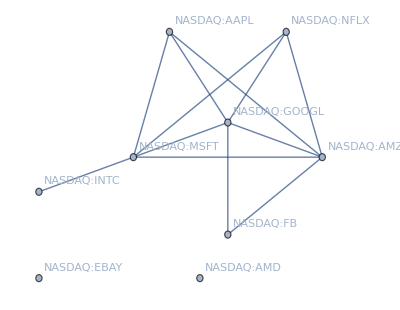

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX","NASDAQ:INTC","NASDAQ:AMD"}
r=(FinancialData[#1,"Return",{{2018},{2019}}]&)/@dji
pos=Position[r,{}]
r=(#1["Values"]&)/@Delete[r,pos]
dji=Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:=ReplacePart[cor,{i_,i_}->0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[0.58],GraphLayout->"RadialEmbedding",VertexLabels->"Name",ImageSize->Full]
stocks=First[FindClique[g]],DateListPlot[(FinancialData[#1,"CumulativeReturn",{{2018},{2019}}]&)/@stocks,Joined->True,AspectRatio->1/5,ImageSize->Full]
```

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

{{1.,0.638328,0.76617,0.634411,0.440314,0.737568,0.615193,0.514946,0.422996},{0.638328,1.,0.680435,0.450426,0.362342,0.639864,0.52214,0.516637,0.419438},{0.76617,0.680435,1.,0.529213,0.467707,0.758334,0.635409,0.586236,0.421029},{0.634411,0.450426,0.529213,1.,0.318276,0.584164,0.464231,0.370161,0.31408},{0.440314,0.362342,0.467707,0.318276,1.,0.387172,0.395068,0.342146,0.2884},{0.737568,0.639864,0.758334,0.584164,0.387172,1.,0.709716,0.449993,0.485324},{0.615193,0.52214,0.635409,0.464231,0.395068,0.709716,1.,0.465024,0.428727},{0.514946,0.516637,0.586236,0.370161,0.342146,0.449993,0.465024,1.,0.333938},{0.422996,0.419438,0.421029,0.31408,0.2884,0.485324,0.428727,0.333938,1.}}

-Graphics-

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:AMZN}

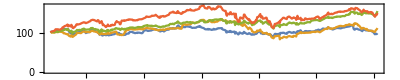

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX","NASDAQ:INTC","NASDAQ:AMD"}
r=(FinancialData[#1,"Return",{{2018},{2019}}]&)/@dji
pos=Position[r,{}]
r=(#1["Values"]&)/@Delete[r,pos]
dji=Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:=ReplacePart[cor,{i_,i_}->0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[0.58],GraphLayout->"RadialEmbedding",VertexLabels->"Name",ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[(FinancialData[#1,"CumulativeReturn",{{2018},{2019}}]&)/@stocks,Joined->True,AspectRatio->1/5,ImageSize->Full]
```

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX","NASDAQ:INTC","NASDAQ:AMD"}
r=(FinancialData[#1,"Return",{{2018},{2019}}]&)/@dji
pos=Position[r,{}]
r=(#1["Values"]&)/@Delete[r,pos]
dji=Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:=ReplacePart[cor,{i_,i_}->0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[0.58],GraphLayout->"RadialEmbedding",VertexLabels->"Name",ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[(FinancialData[#1,"CumulativeReturn",{{2018},{2019}}]&)/@stocks,Joined->True,AspectRatio->1/5,ImageSize->Full]
```

```mathematica
FinancialData["NASDAQ:GOOG", "CumulativeReturn", {2019}]
```

TimeSeries[…]

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

{{1.,0.574545,0.619424,0.666229,0.263111,0.739606,0.523622,0.334568,0.444148},{0.574545,1.,0.653738,0.471376,0.378593,0.611196,0.460038,0.482513,0.54076},{0.619424,0.653738,1.,0.468871,0.422319,0.70866,0.506111,0.43577,0.499053},{0.666229,0.471376,0.468871,1.,0.224212,0.598538,0.403758,0.23943,0.403536},{0.263111,0.378593,0.422319,0.224212,1.,0.319981,0.27824,0.268002,0.34328},{0.739606,0.611196,0.70866,0.598538,0.319981,1.,0.610312,0.306853,0.559522},{0.523622,0.460038,0.506111,0.403758,0.27824,0.610312,1.,0.281581,0.425936},{0.334568,0.482513,0.43577,0.23943,0.268002,0.306853,0.281581,1.,0.350019},{0.444148,0.54076,0.499053,0.403536,0.34328,0.559522,0.425936,0.350019,1.}}

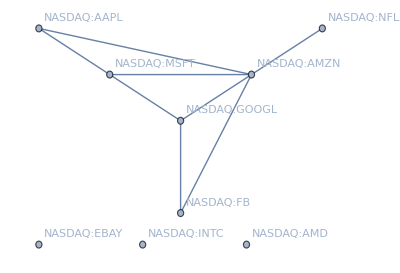

{NASDAQ:GOOGL,NASDAQ:MSFT,NASDAQ:AMZN}

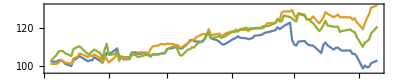

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX","NASDAQ:INTC","NASDAQ:AMD"}
r=(FinancialData[#1,"Return",{2019}]&)/@dji
pos=Position[r,{}]
r=(#1["Values"]&)/@Delete[r,pos]
dji=Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:=ReplacePart[cor,{i_,i_}->0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[0.58],GraphLayout->"RadialEmbedding",VertexLabels->"Name",ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[(FinancialData[#1,"CumulativeReturn",{2019}]&)/@stocks,Joined->True,AspectRatio->1/5,ImageSize->Full]
```

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

{{1.,0.581376,0.727921,0.642666,0.384852,0.688434,0.530738,0.48737,0.239685},{0.581376,1.,0.59529,0.436946,0.323161,0.544567,0.428342,0.479205,0.308557},{0.727921,0.59529,1.,0.525524,0.412343,0.662929,0.502638,0.576487,0.236022},{0.642666,0.436946,0.525524,1.,0.222235,0.590459,0.420265,0.369961,0.213472},{0.384852,0.323161,0.412343,0.222235,1.,0.293451,0.312655,0.298377,0.222798},{0.688434,0.544567,0.662929,0.590459,0.293451,1.,0.549292,0.421982,0.295484},{0.530738,0.428342,0.502638,0.420265,0.312655,0.549292,1.,0.383927,0.27866},{0.48737,0.479205,0.576487,0.369961,0.298377,0.421982,0.383927,1.,0.275181},{0.239685,0.308557,0.236022,0.213472,0.222798,0.295484,0.27866,0.275181,1.}}

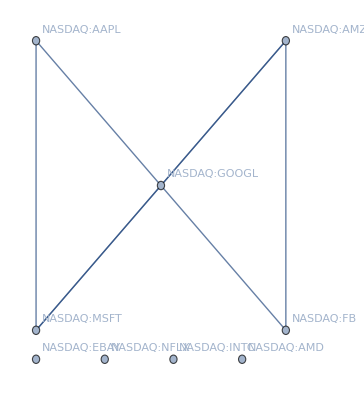

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT}

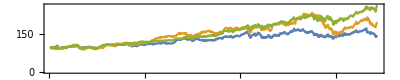

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks]
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX","NASDAQ:INTC","NASDAQ:AMD"}
r=(FinancialData[#1,"Return",{{2016}, {2019}}]&)/@dji
pos=Position[r,{}]
r=(#1["Values"]&)/@Delete[r,pos]
dji=Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:=ReplacePart[cor,{i_,i_}->0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[0.58],GraphLayout->"RadialEmbedding",VertexLabels->"Name",ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[(FinancialData[#1,"CumulativeReturn",{{2016}, {2019}}]&)/@stocks,Joined->True,AspectRatio->1/5,ImageSize->Full]
```

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks,timeRange]
timeRange={{2010}, {2019}}
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX","NASDAQ:INTC","NASDAQ:AMD"}
r=(FinancialData[#1,"Return",timerange]&)/@dji
pos=Position[r,{}]
r=(#1["Values"]&)/@Delete[r,pos]
dji=Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:=ReplacePart[cor,{i_,i_}->0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[0.58],GraphLayout->"RadialEmbedding",VertexLabels->"Name",ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[(FinancialData[#1,"CumulativeReturn",timerange]&)/@stocks,Joined->True,AspectRatio->1/5,ImageSize->Full]
```

{{2010},{2019}}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

FinancialData::notdate: timerange is not a valid date range for FinancialData.

General::stop: Further output of FinancialData::notdate will be suppressed during this calculation.

{FinancialData[NASDAQ:GOOGL,Return,timerange],FinancialData[NASDAQ:AAPL,Return,timerange],FinancialData[NASDAQ:MSFT,Return,timerange],FinancialData[NASDAQ:FB,Return,timerange],FinancialData[NASDAQ:EBAY,Return,timerange],FinancialData[NASDAQ:AMZN,Return,timerange],FinancialData[NASDAQ:NFLX,Return,timerange],FinancialData[NASDAQ:INTC,Return,timerange],FinancialData[NASDAQ:AMD,Return,timerange]}

{}

{FinancialData[NASDAQ:GOOGL,Return,timerange][Values],FinancialData[NASDAQ:AAPL,Return,timerange][Values],FinancialData[NASDAQ:MSFT,Return,timerange][Values],FinancialData[NASDAQ:FB,Return,timerange][Values],FinancialData[NASDAQ:EBAY,Return,timerange][Values],FinancialData[NASDAQ:AMZN,Return,timerange][Values],FinancialData[NASDAQ:NFLX,Return,timerange][Values],FinancialData[NASDAQ:INTC,Return,timerange][Values],FinancialData[NASDAQ:AMD,Return,timerange][Values]}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

Transpose::nmtx: The first two levels of {FinancialData[NASDAQ:GOOGL,Return,timerange][Values],FinancialData[NASDAQ:AAPL,Return,timerange][Values],FinancialData[NASDAQ:MSFT,Return,timerange][Values],FinancialData[NASDAQ:FB,Return,timerange][Values],FinancialData[NASDAQ:EBAY,Return,timerange][Values],FinancialData[NASDAQ:AMZN,Return,timerange][Values],FinancialData[NASDAQ:NFLX,Return,timerange][Values],FinancialData[NASDAQ:INTC,Return,timerange][Values],FinancialData[NASDAQ:AMD,Return,timerange][Values]} cannot be transposed.

Correlation::shlen: The argument Transpose[{FinancialData[NASDAQ:GOOGL,Return,timerange][Values],FinancialData[NASDAQ:AAPL,Return,timerange][Values],FinancialData[NASDAQ:MSFT,Return,timerange][Values],FinancialData[NASDAQ:FB,Return,timerange][Values],FinancialData[NASDAQ:EBAY,Return,timerange][Values],FinancialData[NASDAQ:AMZN,Return,timerange][Values],FinancialData[NASDAQ:NFLX,Return,timerange][Values],FinancialData[NASDAQ:INTC,Return,timerange][Values],FinancialData[NASDAQ:AMD,Return,timerange][Values]}] should have at least two elements.

Correlation[Transpose[{FinancialData[NASDAQ:GOOGL,Return,timerange][Values],FinancialData[NASDAQ:AAPL,Return,timerange][Values],FinancialData[NASDAQ:MSFT,Return,timerange][Values],FinancialData[NASDAQ:FB,Return,timerange][Values],FinancialData[NASDAQ:EBAY,Return,timerange][Values],FinancialData[NASDAQ:AMZN,Return,timerange][Values],FinancialData[NASDAQ:NFLX,Return,timerange][Values],FinancialData[NASDAQ:INTC,Return,timerange][Values],FinancialData[NASDAQ:AMD,Return,timerange][Values]}]]

Correlation::shlen: The argument Transpose[0] should have at least two elements.

AdjacencyGraph::matsq: Argument Correlation[Transpose[0]] at position 2 is not a non-empty square matrix.

AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FindClique::graph: A graph object is expected at position 1 in FindClique[AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]].

AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FinancialData::notdate: timerange is not a valid date range for FinancialData.

General::stop: Further output of FinancialData::notdate will be suppressed during this calculation.

AdjacencyGraph::argt: AdjacencyGraph called with 5 arguments; 1 or 2 arguments are expected.

$Aborted

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks,timeRange]
timeRange={{2010}, {2019}}
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX","NASDAQ:INTC","NASDAQ:AMD"}
r=(FinancialData[#1,"Return",timeRange]&)/@dji
pos=Position[r,{}]
r=(#1["Values"]&)/@Delete[r,pos]
dji=Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:=ReplacePart[cor,{i_,i_}->0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[0.58],GraphLayout->"RadialEmbedding",VertexLabels->"Name",ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[(FinancialData[#1,"CumulativeReturn",timeRange]&)/@stocks,Joined->True,AspectRatio->1/5,ImageSize->Full]
```

{{2010},{2019}}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

General::stop: Further output of FinancialData::dlfail will be suppressed during this calculation.

{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{}

{$Failed[Values],$Failed[Values],$Failed[Values],$Failed[Values],$Failed[Values],$Failed[Values],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

Transpose::nmtx: The first two levels of {$Failed[Values],«8»} cannot be transposed.

Correlation::shlen: The argument Transpose[{$Failed[Values],«7»,StructuredArray[QuantityArray,{2373},StructuredArray`StructuredData[QuantityArray,{0.103093,-1.44181,-1.04493,-0.422386,-3.07529,-5.36105,5.78035,-1.63934,-1.77778,1.92308,-1.55383,1.35287,-12.3471,2.41117,0.247831,1.23609,«2341»,-1.82078,-2.98182,2.51124,0.219378,-3.83072,0.30349,9.79576,-3.23803,-0.213599,-2.21192,0.620212,7.21537,-0.236726,7.86441,1.85418,2.53008},Percent,{{1}}]]}] should have at least two elements.

Correlation[Transpose[{$Failed[Values],$Failed[Values],$Failed[Values],$Failed[Values],$Failed[Values],$Failed[Values],QuantityArray[…],QuantityArray[…],QuantityArray[…]}]]

Correlation::shlen: The argument Transpose[0] should have at least two elements.

AdjacencyGraph::matsq: Argument Correlation[Transpose[0]] at position 2 is not a non-empty square matrix.

AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FindClique::graph: A graph object is expected at position 1 in FindClique[AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]].

AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FinancialData::notent: Correlation[Transpose[0]] is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: GraphLayout→RadialEmbedding is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: VertexLabels→Name is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

AdjacencyGraph::argt: AdjacencyGraph called with 5 arguments; 1 or 2 arguments are expected.

DateListPlot::ldata: AdjacencyGraph[{TemporalData[TimeSeries,{«1»},True,12.],«7»,TemporalData[TimeSeries,{«1»},True,12.]},Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]] is not a valid dataset or list of datasets.

DateListPlot[AdjacencyGraph[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]},Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]],Joined→True,AspectRatio→1/5,ImageSize→Full]

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks,timeRange]
timeRange={{2010}, {2019}}
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX","NASDAQ:INTC","NASDAQ:AMD"}
r=(FinancialData[#1,"Return",timeRange]&)/@dji
pos=Position[r,{}]
r=(#1["Values"]&)/@Delete[r,pos]
dji=Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:=ReplacePart[cor,{i_,i_}->0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[0.58],GraphLayout->"RadialEmbedding",VertexLabels->"Name",ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[(FinancialData[#1,"CumulativeReturn",timeRange]&)/@stocks,Joined->True,AspectRatio->1/5,ImageSize->Full]
```

{{2010},{2019}}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

{TimeSeries[…],TimeSeries[…],TimeSeries[…],$Failed,TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],$Failed[Values],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

Transpose::nmtx: The first two levels of {«1»} cannot be transposed.

Correlation::shlen: The argument Transpose[{StructuredArray[QuantityArray,{2373},«1»],«7»,StructuredArray[QuantityArray,{2373},StructuredArray`StructuredData[QuantityArray,{0.103093,-1.44181,-1.04493,-0.422386,-3.07529,-5.36105,5.78035,-1.63934,-1.77778,1.92308,-1.55383,1.35287,-12.3471,2.41117,0.247831,1.23609,«2342»,-2.98182,2.51124,0.219378,-3.83072,0.30349,9.79576,-3.23803,-0.213599,-2.21192,0.620212,7.21537,-0.236726,7.86441,1.85418,2.53008},Percent,{{1}}]]}] should have at least two elements.

Correlation[Transpose[{QuantityArray[…],QuantityArray[…],QuantityArray[…],$Failed[Values],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}]]

Correlation::shlen: The argument Transpose[0] should have at least two elements.

AdjacencyGraph::matsq: Argument Correlation[Transpose[0]] at position 2 is not a non-empty square matrix.

AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FindClique::graph: A graph object is expected at position 1 in FindClique[AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]].

AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FinancialData::notent: Correlation[Transpose[0]] is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: GraphLayout→RadialEmbedding is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: VertexLabels→Name is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

AdjacencyGraph::argt: AdjacencyGraph called with 5 arguments; 1 or 2 arguments are expected.

DateListPlot::ldata: AdjacencyGraph[{TemporalData[TimeSeries,{«1»},True,12.],«7»,TemporalData[TimeSeries,{«1»},True,12.]},Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]] is not a valid dataset or list of datasets.

DateListPlot[AdjacencyGraph[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]},Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]],Joined→True,AspectRatio→1/5,ImageSize→Full]

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks,timeRange]
timeRange={{2012}, {2019}}
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX","NASDAQ:INTC","NASDAQ:AMD"}
r=(FinancialData[#1,"Return",timeRange]&)/@dji
pos=Position[r,{}]
r=(#1["Values"]&)/@Delete[r,pos]
dji=Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:=ReplacePart[cor,{i_,i_}->0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[0.58],GraphLayout->"RadialEmbedding",VertexLabels->"Name",ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[(FinancialData[#1,"CumulativeReturn",timeRange]&)/@stocks,Joined->True,AspectRatio->1/5,ImageSize->Full]
```

{{2012},{2019}}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

General::stop: Further output of FinancialData::dlfail will be suppressed during this calculation.

{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{}

{$Failed[Values],$Failed[Values],$Failed[Values],$Failed[Values],$Failed[Values],$Failed[Values],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

Transpose::nmtx: The first two levels of {$Failed[Values],«7»,StructuredArray[QuantityArray,{1869},StructuredArray`StructuredData[QuantityArray,{-0.364964,-1.11022×10^-14,-0.549451,2.94659,2.14669,1.75131,0.172117,-2.74914,1.23675,4.18848,4.1876,3.21543,1.55763,0.153374,3.06279,0.594354,0.738552,«1836»,-1.82078,-2.98182,2.51124,0.219378,-3.83072,0.30349,9.79576,-3.23803,-0.213599,-2.21192,0.620212,7.21537,-0.236726,7.86441,1.85418,2.53008},Percent,{{1}}]]} cannot be transposed.

Correlation::shlen: The argument Transpose[{«1»}] should have at least two elements.

Correlation[Transpose[{$Failed[Values],$Failed[Values],$Failed[Values],$Failed[Values],$Failed[Values],$Failed[Values],QuantityArray[…],QuantityArray[…],QuantityArray[…]}]]

Correlation::shlen: The argument Transpose[0] should have at least two elements.

AdjacencyGraph::matsq: Argument Correlation[Transpose[0]] at position 2 is not a non-empty square matrix.

AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FindClique::graph: A graph object is expected at position 1 in FindClique[AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]].

AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FinancialData::notent: Correlation[Transpose[0]] is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: GraphLayout→RadialEmbedding is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: VertexLabels→Name is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

AdjacencyGraph::argt: AdjacencyGraph called with 5 arguments; 1 or 2 arguments are expected.

DateListPlot::ldata: AdjacencyGraph[{«1»},Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]] is not a valid dataset or list of datasets.

DateListPlot[AdjacencyGraph[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]},Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]],Joined→True,AspectRatio→1/5,ImageSize→Full]

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks,timeRange]
timeRange={{2014}, {2019}}
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX","NASDAQ:INTC","NASDAQ:AMD"}
r=(FinancialData[#1,"Return",timeRange]&)/@dji
pos=Position[r,{}]
r=(#1["Values"]&)/@Delete[r,pos]
dji=Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:=ReplacePart[cor,{i_,i_}->0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[0.58],GraphLayout->"RadialEmbedding",VertexLabels->"Name",ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[(FinancialData[#1,"CumulativeReturn",timeRange]&)/@stocks,Joined->True,AspectRatio->1/5,ImageSize->Full]
```

{{2014},{2019}}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],Missing[],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],Missing[][Values],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

Transpose::nmtx: The first two levels of {«1»} cannot be transposed.

Correlation::shlen: The argument Transpose[{«1»}] should have at least two elements.

Correlation[Transpose[{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],Missing[][Values],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}]]

Correlation::shlen: The argument Transpose[0] should have at least two elements.

AdjacencyGraph::matsq: Argument Correlation[Transpose[0]] at position 2 is not a non-empty square matrix.

AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FindClique::graph: A graph object is expected at position 1 in FindClique[AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]].

AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FinancialData::notent: Correlation[Transpose[0]] is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: GraphLayout→RadialEmbedding is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: VertexLabels→Name is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

AdjacencyGraph::argt: AdjacencyGraph called with 5 arguments; 1 or 2 arguments are expected.

DateListPlot::ldata: AdjacencyGraph[«1»] is not a valid dataset or list of datasets.

DateListPlot[AdjacencyGraph[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],{},TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]},Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]],Joined→True,AspectRatio→1/5,ImageSize→Full]

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks,timeRange]
timeRange={{2018}, {2019}}
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX","NASDAQ:INTC","NASDAQ:AMD"}
r=(FinancialData[#1,"Return",timeRange]&)/@dji
pos=Position[r,{}]
r=(#1["Values"]&)/@Delete[r,pos]
dji=Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:=ReplacePart[cor,{i_,i_}->0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[0.58],GraphLayout->"RadialEmbedding",VertexLabels->"Name",ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[(FinancialData[#1,"CumulativeReturn",timeRange]&)/@stocks,Joined->True,AspectRatio->1/5,ImageSize->Full]
```

{{2018},{2019}}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

{{1.,0.638328,0.76617,0.634411,0.440314,0.737568,0.615193,0.514946,0.422996},{0.638328,1.,0.680435,0.450426,0.362342,0.639864,0.52214,0.516637,0.419438},{0.76617,0.680435,1.,0.529213,0.467707,0.758334,0.635409,0.586236,0.421029},{0.634411,0.450426,0.529213,1.,0.318276,0.584164,0.464231,0.370161,0.31408},{0.440314,0.362342,0.467707,0.318276,1.,0.387172,0.395068,0.342146,0.2884},{0.737568,0.639864,0.758334,0.584164,0.387172,1.,0.709716,0.449993,0.485324},{0.615193,0.52214,0.635409,0.464231,0.395068,0.709716,1.,0.465024,0.428727},{0.514946,0.516637,0.586236,0.370161,0.342146,0.449993,0.465024,1.,0.333938},{0.422996,0.419438,0.421029,0.31408,0.2884,0.485324,0.428727,0.333938,1.}}

-Graphics-

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:AMZN}

-Graphics-

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks,timeRange]
timeRange={{2018}, {2019}}
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX","NASDAQ:INTC","NASDAQ:AMD"}
r=(FinancialData[#1,"Return",timeRange]&)/@dji
pos=Position[r,{}]
r=(#1["Values"]&)/@Delete[r,pos]
dji=Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:=ReplacePart[cor,{i_,i_}->0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[0.58],GraphLayout->"RadialEmbedding",VertexLabels->"Name",ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[(FinancialData[#1,"CumulativeReturn",timeRange]&)/@stocks,Joined->True,AspectRatio->1/5,ImageSize->Full, PlotLegends->"Expressions"]
```

{{2018},{2019}}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

{{1.,0.638328,0.76617,0.634411,0.440314,0.737568,0.615193,0.514946,0.422996},{0.638328,1.,0.680435,0.450426,0.362342,0.639864,0.52214,0.516637,0.419438},{0.76617,0.680435,1.,0.529213,0.467707,0.758334,0.635409,0.586236,0.421029},{0.634411,0.450426,0.529213,1.,0.318276,0.584164,0.464231,0.370161,0.31408},{0.440314,0.362342,0.467707,0.318276,1.,0.387172,0.395068,0.342146,0.2884},{0.737568,0.639864,0.758334,0.584164,0.387172,1.,0.709716,0.449993,0.485324},{0.615193,0.52214,0.635409,0.464231,0.395068,0.709716,1.,0.465024,0.428727},{0.514946,0.516637,0.586236,0.370161,0.342146,0.449993,0.465024,1.,0.333938},{0.422996,0.419438,0.421029,0.31408,0.2884,0.485324,0.428727,0.333938,1.}}

-Graphics-

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:AMZN}

-Graphics-

{{2017},{2019}}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

{}

{QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…],QuantityArray[…]}

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD}

{{1.,0.609091,0.737103,0.645093,0.435811,0.721631,0.584371,0.488456,0.368393},{0.609091,1.,0.63408,0.465592,0.366688,0.614037,0.483227,0.484594,0.381625},{0.737103,0.63408,1.,0.529417,0.452163,0.730838,0.591609,0.569659,0.36218},{0.645093,0.465592,0.529417,1.,0.330871,0.592586,0.46854,0.368703,0.30093},{0.435811,0.366688,0.452163,0.330871,1.,0.367139,0.380467,0.313798,0.265659},{0.721631,0.614037,0.730838,0.592586,0.367139,1.,0.637449,0.446155,0.410816},{0.584371,0.483227,0.591609,0.46854,0.380467,0.637449,1.,0.420083,0.36878},{0.488456,0.484594,0.569659,0.368703,0.313798,0.446155,0.420083,1.,0.272675},{0.368393,0.381625,0.36218,0.30093,0.265659,0.410816,0.36878,0.272675,1.}}

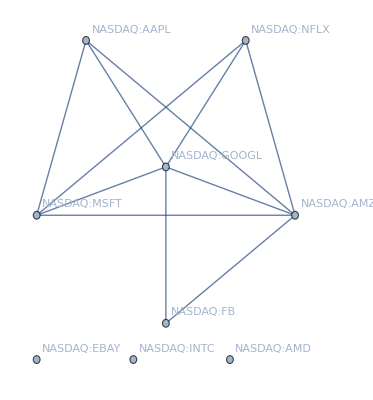

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:AMZN}

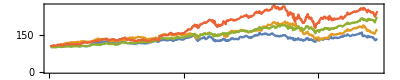

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks,timeRange]
timeRange={{2017}, {2019}}
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX","NASDAQ:INTC","NASDAQ:AMD"}
r=(FinancialData[#1,"Return",timeRange]&)/@dji
pos=Position[r,{}]
r=(#1["Values"]&)/@Delete[r,pos]
dji=Delete[dji,pos]
cor=Correlation[Transpose[r]]
portfolioMatrix[θ_]:=ReplacePart[cor,{i_,i_}->0]/.{x_/;x>θ->1,x_/;x<θ->0}
g=AdjacencyGraph[dji,portfolioMatrix[0.58],GraphLayout->"RadialEmbedding",VertexLabels->"Name",ImageSize->Full]
stocks=First[FindClique[g]]
DateListPlot[(FinancialData[#1,"CumulativeReturn",timeRange]&)/@stocks,Joined->True,AspectRatio->1/5,ImageSize->Full]
```

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks,timeRange]
timeRange={{2016}, {2019}};
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX","NASDAQ:INTC","NASDAQ:AMD"};
r=(FinancialData[#1,"Return",timeRange]&)/@dji;
pos=Position[r,{}];
r=(#1["Values"]&)/@Delete[r,pos];
dji=Delete[dji,pos];
cor=Correlation[Transpose[r]];
portfolioMatrix[θ_]:=ReplacePart[cor,{i_,i_}->0]/.{x_/;x>θ->1,x_/;x<θ->0};
g=AdjacencyGraph[dji,portfolioMatrix[0.58],GraphLayout->"RadialEmbedding",VertexLabels->"Name",ImageSize->Full];
stocks=First[FindClique[g]]
DateListPlot[(FinancialData[#1,"CumulativeReturn",timeRange]&)/@stocks,Joined->True,AspectRatio->1/5,ImageSize->Full]
```

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT}

-Graphics-

```mathematica
Show[%166,Axes->True,AxesStyle->Black]
```

-Graphics-

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks,timeRange]
timeRange={{2016}, {2019}};
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX","NASDAQ:INTC","NASDAQ:AMD"};
r=(FinancialData[#1,"Return",timeRange]&)/@dji;
pos=Position[r,{}];
r=(#1["Values"]&)/@Delete[r,pos];
dji=Delete[dji,pos];
cor=Correlation[Transpose[r]];
portfolioMatrix[θ_]:=ReplacePart[cor,{i_,i_}->0]/.{x_/;x>θ->1,x_/;x<θ->0};
g=AdjacencyGraph[dji,portfolioMatrix[0.58],GraphLayout->"RadialEmbedding",VertexLabels->"Name",ImageSize->Full];
stocks=First[FindClique[g]]
DateListPlot[(FinancialData[#1,"CumulativeReturn",timeRange]&)/@stocks,Joined->True,AspectRatio->1/5,ImageSize->Full,PlotLegends->stocks]
```

{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT}

-Graphics-

{NASDAQ:GOOGL,NASDAQ:MSFT,NASDAQ:AMZN}

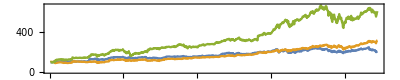

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks,timeRange]
timeRange={{2015}, {2019}};
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX","NASDAQ:INTC","NASDAQ:AMD"};
r=(FinancialData[#1,"Return",timeRange]&)/@dji;
pos=Position[r,{}];
r=(#1["Values"]&)/@Delete[r,pos];
dji=Delete[dji,pos];
cor=Correlation[Transpose[r]];
portfolioMatrix[θ_]:=ReplacePart[cor,{i_,i_}->0]/.{x_/;x>θ->1,x_/;x<θ->0};
g=AdjacencyGraph[dji,portfolioMatrix[0.58],GraphLayout->"RadialEmbedding",VertexLabels->"Name",ImageSize->Full];
stocks=First[FindClique[g]]
DateListPlot[(FinancialData[#1,"CumulativeReturn",timeRange]&)/@stocks,Joined->True,AspectRatio->1/5,ImageSize->Full,PlotLegends->stocks]
```

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks,timeRange]
timeRange={{2014}, {2019}};
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX","NASDAQ:INTC","NASDAQ:AMD"};
r=(FinancialData[#1,"Return",timeRange]&)/@dji;
pos=Position[r,{}];
r=(#1["Values"]&)/@Delete[r,pos];
dji=Delete[dji,pos];
cor=Correlation[Transpose[r]];
portfolioMatrix[θ_]:=ReplacePart[cor,{i_,i_}->0]/.{x_/;x>θ->1,x_/;x<θ->0};
g=AdjacencyGraph[dji,portfolioMatrix[0.58],GraphLayout->"RadialEmbedding",VertexLabels->"Name",ImageSize->Full];
stocks=First[FindClique[g]]
DateListPlot[(FinancialData[#1,"CumulativeReturn",timeRange]&)/@stocks,Joined->True,AspectRatio->1/5,ImageSize->Full,PlotLegends->stocks]
```

Transpose::nmtx: The first two levels of {«1»} cannot be transposed.

Correlation::shlen: The argument Transpose[{«1»}] should have at least two elements.

Correlation::shlen: The argument Transpose[0] should have at least two elements.

AdjacencyGraph::matsq: Argument Correlation[Transpose[0]] at position 2 is not a non-empty square matrix.

FindClique::graph: A graph object is expected at position 1 in FindClique[AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]].

AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]

FinancialData::notent: Correlation[Transpose[0]] is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: GraphLayout→RadialEmbedding is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: VertexLabels→Name is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

AdjacencyGraph::argt: AdjacencyGraph called with 5 arguments; 1 or 2 arguments are expected.

DateListPlot::ldata: AdjacencyGraph[«1»] is not a valid dataset or list of datasets.

DateListPlot[AdjacencyGraph[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],{},TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]},Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]],Joined→True,AspectRatio→1/5,ImageSize→Full,PlotLegends→AdjacencyGraph[{NASDAQ:GOOGL,NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:FB,NASDAQ:EBAY,NASDAQ:AMZN,NASDAQ:NFLX,NASDAQ:INTC,NASDAQ:AMD},Correlation[Transpose[0]],GraphLayout→RadialEmbedding,VertexLabels→Name,ImageSize→Full]]

```mathematica
Clear[dji,r,pos,cor,portfolioMatrix,g,stocks,timeRange]
timeRange={{2015}, {2019}};
dji={"NASDAQ:GOOGL","NASDAQ:AAPL","NASDAQ:MSFT","NASDAQ:FB","NASDAQ:EBAY","NASDAQ:AMZN","NASDAQ:NFLX","NASDAQ:INTC","NASDAQ:AMD"};
r=(FinancialData[#1,"Return",timeRange]&)/@dji;
pos=Position[r,{}];
r=(#1["Values"]&)/@Delete[r,pos];
dji=Delete[dji,pos];
cor=Correlation[Transpose[r]];
portfolioMatrix[θ_]:=ReplacePart[cor,{i_,i_}->0]/.{x_/;x>θ->1,x_/;x<θ->0};
g=AdjacencyGraph[dji,portfolioMatrix[0.58],GraphLayout->"RadialEmbedding",VertexLabels->"Name",ImageSize->Full];
stocks=First[FindClique[g]]
DateListPlot[(FinancialData[#1,"CumulativeReturn",timeRange]&)/@stocks,Joined->True,AspectRatio->1/5,ImageSize->Full,PlotLegends->stocks]
```

{NASDAQ:GOOGL,NASDAQ:MSFT,NASDAQ:AMZN}

-Graphics-

```mathematica
With[{stock1="NASDAQ:GOOGL", stock2="NASDAQ:AMZN"},
With[{
list1=FinancialData[stock1, "Price", {2019}],
list2= FinancialData[stock2, "Price", {2019}]
},
Correlation[
Differences@
list1["Values"],
Differences@
list2["Values"]
]
]]
```

0.701939

```mathematica
With[{stock1="NASDAQ:GOOGL", stock2="NASDAQ:AMZN"},
With[{
list1=FinancialData[stock1, "Price", {2019}],
list2= FinancialData[stock2, "Price", {2019}]
},
Correlation[
Standardize@
Differences@
list1["Values"],
Standardize@
Differences@
list2["Values"]
]
]]
```

0.701939

```mathematica
With[{stock1="NASDAQ:GOOGL", stock2="NASDAQ:MFTS"},
With[{
list1=FinancialData[stock1, "Price", {2019}],
list2= FinancialData[stock2, "Price", {2019}]
},
Correlation[
Standardize@
Differences@
list1["Values"],
Standardize@
Differences@
list2["Values"]
]
]]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

Standardize::vectmat: The first argument is expected to be a vector or matrix.

Correlation::vctmat: The arguments to Correlation are not a pair of vectors or a pair of matrices of equal length.

Correlation[{-1.5259,2.71005,-0.124779,0.475835,-0.206074,-0.159479,-0.75699,-0.6845,1.79876,0.141871,0.484121,0.410083,-1.49793,0.285815,-0.0346929,0.893167,-1.13445,-0.520881,1.43269,1.43114,-0.389888,1.16707,0.527613,-1.51398,-0.892648,-0.196239,-0.0269249,1.3048,0.040907,0.0160484,-0.508973,0.342769,-0.319989,-0.861582,0.625998,0.0264014,0.228861,0.0321025,0.176046,1.12409,0.24025,0.803068,-0.233518,-0.788574,1.50311,0.91802,0.0802586,-0.351573,-0.128926,-0.104073,0.706762,1.22766,0.48878,-1.48809,-0.545221,-0.403869,-0.625991,-0.310666,0.225751,1.13031,0.326203,0.259408,0.433892,-0.427684,-0.177594,-0.302905,0.181223,0.149121,0.666899,0.183296,0.265103,0.412668,0.0554,0.622889,0.857956,-0.559196,0.363994,0.508462,0.95892,-5.04833,-1.34105,-0.366066,1.1795,0.188984,-0.769417,-0.431824,-0.158961,-0.0305466,-1.62116,-0.620815,2.36521,0.695891,-0.827407,-1.26234,0.49292,0.0595462,-0.557647,-0.361926,0.0357305,-1.02935,0.0626559,-0.785471,-3.52192,0.802038,-0.523472,0.148084,1.05368,0.731621},Standardize[Differences[$Failed[Values]]]]

```mathematica
With[{stock1="NASDAQ:GOOGL", stock2="NASDAQ:MSFT"},
With[{
list1=FinancialData[stock1, "Price", {2019}],
list2= FinancialData[stock2, "Price", {2019}]
},
Correlation[
Standardize@
Differences@
list1["Values"],
Standardize@
Differences@
list2["Values"]
]
]]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

Standardize::vectmat: The first argument is expected to be a vector or matrix.

Correlation::vctmat: The arguments to Correlation are not a pair of vectors or a pair of matrices of equal length.

Correlation[{-1.5259,2.71005,-0.124779,0.475835,-0.206074,-0.159479,-0.75699,-0.6845,1.79876,0.141871,0.484121,0.410083,-1.49793,0.285815,-0.0346929,0.893167,-1.13445,-0.520881,1.43269,1.43114,-0.389888,1.16707,0.527613,-1.51398,-0.892648,-0.196239,-0.0269249,1.3048,0.040907,0.0160484,-0.508973,0.342769,-0.319989,-0.861582,0.625998,0.0264014,0.228861,0.0321025,0.176046,1.12409,0.24025,0.803068,-0.233518,-0.788574,1.50311,0.91802,0.0802586,-0.351573,-0.128926,-0.104073,0.706762,1.22766,0.48878,-1.48809,-0.545221,-0.403869,-0.625991,-0.310666,0.225751,1.13031,0.326203,0.259408,0.433892,-0.427684,-0.177594,-0.302905,0.181223,0.149121,0.666899,0.183296,0.265103,0.412668,0.0554,0.622889,0.857956,-0.559196,0.363994,0.508462,0.95892,-5.04833,-1.34105,-0.366066,1.1795,0.188984,-0.769417,-0.431824,-0.158961,-0.0305466,-1.62116,-0.620815,2.36521,0.695891,-0.827407,-1.26234,0.49292,0.0595462,-0.557647,-0.361926,0.0357305,-1.02935,0.0626559,-0.785471,-3.52192,0.802038,-0.523472,0.148084,1.05368,0.731621},Standardize[Differences[$Failed[Values]]]]

```mathematica
With[{stock1="NASDAQ:GOOGL", stock2="NASDAQ:AAPL"},
With[{
list1=FinancialData[stock1, "Price", {2019}],
list2= FinancialData[stock2, "Price", {2019}]
},
Correlation[
Standardize@
Differences@
list1["Values"],
Standardize@
Differences@
list2["Values"]
]
]]
```

FinancialData::dlfail: Internet download of data for FinancialData failed. Use Help > Internet Connectivity... to test or reconfigure internet connectivity.

Standardize::vectmat: The first argument is expected to be a vector or matrix.

Correlation::vctmat: The arguments to Correlation are not a pair of vectors or a pair of matrices of equal length.

Correlation[{-1.5259,2.71005,-0.124779,0.475835,-0.206074,-0.159479,-0.75699,-0.6845,1.79876,0.141871,0.484121,0.410083,-1.49793,0.285815,-0.0346929,0.893167,-1.13445,-0.520881,1.43269,1.43114,-0.389888,1.16707,0.527613,-1.51398,-0.892648,-0.196239,-0.0269249,1.3048,0.040907,0.0160484,-0.508973,0.342769,-0.319989,-0.861582,0.625998,0.0264014,0.228861,0.0321025,0.176046,1.12409,0.24025,0.803068,-0.233518,-0.788574,1.50311,0.91802,0.0802586,-0.351573,-0.128926,-0.104073,0.706762,1.22766,0.48878,-1.48809,-0.545221,-0.403869,-0.625991,-0.310666,0.225751,1.13031,0.326203,0.259408,0.433892,-0.427684,-0.177594,-0.302905,0.181223,0.149121,0.666899,0.183296,0.265103,0.412668,0.0554,0.622889,0.857956,-0.559196,0.363994,0.508462,0.95892,-5.04833,-1.34105,-0.366066,1.1795,0.188984,-0.769417,-0.431824,-0.158961,-0.0305466,-1.62116,-0.620815,2.36521,0.695891,-0.827407,-1.26234,0.49292,0.0595462,-0.557647,-0.361926,0.0357305,-1.02935,0.0626559,-0.785471,-3.52192,0.802038,-0.523472,0.148084,1.05368,0.731621},Standardize[Differences[$Failed[Values]]]]

```mathematica
With[{stock1="NASDAQ:GOOGL", stock2="NASDAQ:GOOGL"},
With[{
list1=FinancialData[stock1, "Price", {2019}],
list2= FinancialData[stock2, "Price", {2019}]
},
Correlation[
Standardize@
Differences@
list1["Values"],
Standardize@
Differences@
list2["Values"]
]
]]
```

1.

```mathematica
With[{stock1="NASDAQ:GOOGL", stock2="NASDAQ:AMNZ"},
With[{
list1=FinancialData[stock1, "Price", {2019}],
list2= FinancialData[stock2, "Price", {2019}]
},
Correlation[
Standardize@
Differences@
list1["Values"],
Standardize@
Differences@
list2["Values"]
]
]]
```

FinancialData::notent: NASDAQ:AMNZ is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

Standardize::vectmat: The first argument is expected to be a vector or matrix.

Correlation::vctmat: The arguments to Correlation are not a pair of vectors or a pair of matrices of equal length.

Correlation[{-1.5259,2.71005,-0.124779,0.475835,-0.206074,-0.159479,-0.75699,-0.6845,1.79876,0.141871,0.484121,0.410083,-1.49793,0.285815,-0.0346929,0.893167,-1.13445,-0.520881,1.43269,1.43114,-0.389888,1.16707,0.527613,-1.51398,-0.892648,-0.196239,-0.0269249,1.3048,0.040907,0.0160484,-0.508973,0.342769,-0.319989,-0.861582,0.625998,0.0264014,0.228861,0.0321025,0.176046,1.12409,0.24025,0.803068,-0.233518,-0.788574,1.50311,0.91802,0.0802586,-0.351573,-0.128926,-0.104073,0.706762,1.22766,0.48878,-1.48809,-0.545221,-0.403869,-0.625991,-0.310666,0.225751,1.13031,0.326203,0.259408,0.433892,-0.427684,-0.177594,-0.302905,0.181223,0.149121,0.666899,0.183296,0.265103,0.412668,0.0554,0.622889,0.857956,-0.559196,0.363994,0.508462,0.95892,-5.04833,-1.34105,-0.366066,1.1795,0.188984,-0.769417,-0.431824,-0.158961,-0.0305466,-1.62116,-0.620815,2.36521,0.695891,-0.827407,-1.26234,0.49292,0.0595462,-0.557647,-0.361926,0.0357305,-1.02935,0.0626559,-0.785471,-3.52192,0.802038,-0.523472,0.148084,1.05368,0.731621},Standardize[Differences[Missing[NotAvailable][Values]]]]

```mathematica
With[{stock1="NASDAQ:GOOGL", stock2="NASDAQ:AMZN"},
With[{
list1=FinancialData[stock1, "Price", {2019}],
list2= FinancialData[stock2, "Price", {2019}]
},
Correlation[
Standardize@
Differences@
list1["Values"],
Standardize@
Differences@
list2["Values"]
]
]]
```

0.701939

```mathematica
With[{stock1="NASDAQ:GOOGL", stock2="NASDAQ:AMZN", range={{2018},{2019}}},
With[{
list1=FinancialData[stock1, "Price", range],
list2= FinancialData[stock2, "Price", range]
},
Correlation[
Standardize@
Differences@
list1["Values"],
Standardize@
Differences@
list2["Values"]
]
]]
```

0.719282

```mathematica
With[{stock1="NASDAQ:GOOGL", stock2="NASDAQ:AMZN", range={{2010},{2019}}},
With[{
list1=FinancialData[stock1, "Price", range],
list2= FinancialData[stock2, "Price", range]
},
Correlation[
Standardize@
Differences@
list1["Values"],
Standardize@
Differences@
list2["Values"]
]
]]
```

Correlation::vctmat: The arguments to Correlation are not a pair of vectors or a pair of matrices of equal length.

Correlation[{-0.165373,-0.79446,-0.718366,0.35282,-0.0756152,-0.547091,-0.195907,0.102543,-0.509286,0.338281,-0.381241,0.0932397,-1.63088,-0.516945,0.0859687,-0.0469245,-0.41032,-0.24224,0.117762,-0.123599,0.439188,-0.712647,0.187456,0.0743374,0.112722,-0.128252,0.0634811,-0.190576,0.365421,-0.181462,0.211783,-0.150639,0.0674538,-0.406442,-0.206086,-0.275876,-0.0134831,0.254338,0.37463,0.175244,0.418345,0.435212,-0.11526,-0.142596,0.757413,0.196179,-0.109057,-0.825088,0.0665812,-0.0139682,0.00929736,-0.341887,-0.152677,-0.443761,0.372692,0.237862,-0.0406237,-0.043144,0.175339,-0.0115455,0.0501045,0.0757927,-0.166829,-0.258429,0.160217,-0.0930622,0.284387,0.649723,0.07676,0.274208,-2.22197,-0.0336426,0.208295,-0.0672793,-0.382694,-0.131837,-0.679014,-0.15665,-0.0251143,0.104966,-0.337331,0.206553,-1.2069,0.133078,-0.569385,-0.29972,1.3517,-0.642664,-0.208994,0.234952,-0.193969,-0.0100901,-0.497171,-0.222466,-0.973588,-0.174971,0.216439,-0.0357769,-0.109058,0.695862,-0.265795,-0.18951,0.502191,0.561902,-0.365149,-0.671842,-0.0672793,-0.55339,0.598735,0.0408959,-0.289059,0.686555,0.127748,-0.089187,-0.0338378,-0.587802,-0.143468,-0.235164,-0.36864,-0.148799,-0.0604948,-0.895945,-0.48302,-0.296329,-0.174098,-0.0546777,0.654083,0.277119,0.498798,0.373274,0.617154,0.0722046,0.0987625,-1.70096,0.287586,0.71612,-0.229833,0.323257,0.223224,-0.0842426,0.146163,-0.433099,-0.00039785,-0.0381996,0.238344,-0.0596222,0.76856,0.0549514,-0.413713,0.217504,-0.110996,-0.612131,-0.0183299,-0.305925,-0.0683457,0.207812,-0.43746,-0.719337,-0.320078,0.0680366,-0.646541,0.125226,-0.208025,0.349428,-0.329285,-0.160915,0.469043,0.106517,0.314049,-0.317654,0.268394,0.240283,-0.0333542,0.265971,-0.120689,-0.0212377,-0.0110589,0.409525,0.848141,0.219928,0.0917843,-0.153644,0.638476,0.119993,-0.188639,-0.0061144,-0.123599,-0.0396535,-0.190091,0.738995,-0.219658,-0.24195,0.276149,0.0893616,0.0922694,0.0612507,-0.146376,2.90454,0.757413,-0.510739,-0.0240494,0.163125,-0.00524176,0.161188,0.0704593,-0.134745,0.0709444,-0.268218,0.0316873,-0.00233689,0.190754,0.167003,0.00793663,0.0505896,-0.126018,-0.125536,-0.307475,-0.705767,-0.410805,-0.601372,-0.0396535,0.599704,-0.309415,-0.0125128,-0.429707,0.548818,-0.272483,-0.414198,-1.31217,0.387717,0.331013,0.0258717,0.228553,0.394503,0.133562,0.0152077,0.00299658,0.0854835,-0.0173582,-0.255037,0.0370178,-0.0756152,0.175241,0.357183,0.0859687,-0.0924824,-0.121173,-0.1993,0.069489,-0.135227,-0.268605,0.472141,-0.13959,0.305712,0.183483,0.111269,-0.13959,0.0558225,0.0103623,-0.0401386,0.331882,0.718156,-0.413713,-0.272969,-0.756268,-0.0677644,0.396925,-0.196779,-0.0173611,-0.797948,-0.0619488,0.486683,0.0152077,-0.121173,0.00881223,0.129394,0.166808,-0.122626,-0.034323,0.359606,0.145581,-0.22547,-0.0280251,0.0190887,0.202382,-0.995301,0.0223811,-0.152677,0.0278122,0.131527,-0.644605,-0.0299597,0.394017,-0.465086,-0.466056,0.0000858014,-0.0575855,-0.587898,-0.205601,-0.357396,-0.052255,-0.635879,0.175241,-0.0459542,0.717573,0.00842472,0.203352,0.198022,-0.378236,-0.243887,0.277601,-0.0260846,0.207231,0.213144,-0.231289,-0.933263,0.215469,0.250945,-0.120691,-0.069702,-0.359431,0.243677,0.07676,-2.35079,-0.218687,-0.28896,0.172334,-0.0620464,-0.0338378,0.345552,0.208295,-0.0212363,0.26597,-0.300207,-0.257941,0.0607655,-0.105179,0.018503,0.0840311,0.210233,-0.381238,-0.0508026,-0.298169,-0.571421,0.552694,-0.062919,0.0383756,-0.381626,-0.305052,-0.0377159,0.0370178,-0.106149,0.10293,0.362514,-0.197265,0.0879092,-0.273066,-0.129411,-0.1299,-0.0245316,-0.149867,-0.381919,-0.262983,0.145097,-0.294294,-0.15665,-0.776043,-0.0527402,0.377054,-0.322305,-0.360498,-0.290513,0.352821,0.494922,0.158765,0.395955,0.679188,0.522258,0.110201,0.513922,-0.740179,-0.25998,0.295149,0.174756,-0.483598,3.3005,-0.161498,0.337796,-0.380753,0.533306,0.513922,0.00493415,0.140348,-0.773718,0.149071,-0.383179,0.118052,-0.728544,0.394017,-1.17869,0.0423483,-1.6333,1.29732,-1.21514,0.605037,0.048164,-0.34867,-0.915819,-0.315228,-1.4028,-0.708675,0.320253,0.970371,0.185515,-0.189121,0.299411,0.561417,0.0471967,-0.0188136,-0.441824,-0.403049,-0.160433,0.543485,0.0136606,-0.521891,0.22429,-0.0604934,0.0922694,0.477475,0.168459,-0.0319003,-0.0336455,-0.391613,-0.930841,0.203935,0.278086,0.329945,-0.54079,-0.0963575,-0.635882,-0.978434,0.278086,0.104483,0.454114,-0.0114479,1.03822,0.260154,0.226713,0.477475,1.55448,-0.481178,0.361543,-0.507346,0.112722,0.299411,0.256276,-0.674651,0.121348,0.568203,0.0399256,-0.395295,-0.710127,0.267907,0.583712,-0.0973278,0.559962,0.163128,-0.584023,-0.316198,0.612403,0.194144,0.141318,-0.278397,-0.545635,-0.322017,-0.707704,-0.076973,-0.511227,-0.376295,1.1906,-0.286635,0.767103,0.666202,0.28836,0.225163,-0.122626,-0.0498323,-0.387542,0.520222,-0.1299,-0.0197809,-0.398203,0.0399256,0.280024,-0.231771,0.382868,-0.252126,0.156824,0.135502,0.313465,-0.0580707,0.0995375,0.13841,0.915024,0.107873,-0.481175,-0.467509,-1.36839,0.00154119,0.105353,0.147134,-0.256974,0.14277,0.178634,0.291658,-2.63073,-0.0541926,-0.254164,-0.586348,-0.0988778,0.544937,-0.142498,0.0859687,0.00348171,0.176212,0.512951,0.587587,-0.143954,0.117958,0.0467116,-0.300594,0.273726,-0.149867,-0.235164,0.0152077,-0.122626,0.422611,-0.325309,-0.120206,0.152366,-0.0600082,0.409136,-0.038201,0.169914,-0.0872495,-0.370965,-0.482146,0.0578577,-0.0149355,-0.365637,0.206263,0.581287,-0.118265,0.217989,0.15828,0.402256,-0.0551628,0.283417,0.263065,-0.199303,0.295634,-0.143566,0.39266,-0.388024,-0.379206,0.244065,-0.240012,-0.393745,-0.168766,-0.103143,-0.224503,0.410009,0.698673,-1.31256,-0.930356,0.138309,-0.134257,-0.426799,-0.188541,0.0433186,0.146551,0.378508,0.247553,-0.0551628,-0.522858,-0.0517699,0.105841,0.151009,-0.713038,0.481838,0.222835,-0.208023,0.187361,-0.440371,-0.091027,0.313468,0.833114,-0.316684,-1.13023,0.633728,-0.677171,0.388684,-0.312805,-0.619789,0.104871,-0.327833,-0.388995,-0.509674,0.337213,-0.429219,0.463418,-0.147829,0.0753047,-0.608738,-0.196294,-0.225473,-0.128441,0.230493,0.274306,0.487654,-0.225473,-0.628125,0.274211,-0.555329,0.16264,0.191721,-0.274034,0.735117,-0.0120277,0.322771,0.361546,-0.511712,-0.0314151,-0.240012,-0.540787,-0.0654393,0.259669,-0.108959,0.0558225,0.167488,0.565295,0.827301,0.196567,-0.414683,-0.01193,0.230493,1.01651,-0.162468,0.00260907,-0.0459542,-0.220628,0.574989,0.0412834,-0.142983,0.0510748,-0.0265697,-0.0459542,0.84184,0.390625,-0.0896722,0.230591,0.172334,-0.109057,-0.322499,0.342159,-0.0508026,0.0559202,-0.487476,0.356698,0.492499,-0.337041,0.133562,-0.230319,-0.0459542,0.875767,0.298441,-0.293323,-0.448704,-0.0944199,0.701096,0.148101,-0.016876,0.371237,0.414857,-0.00223632,0.254821,0.715635,-0.0411059,0.177179,0.11408,-0.128347,0.322677,-0.264245,0.235338,0.240284,-0.055648,-0.506864,-0.696073,-0.00708466,0.303289,-0.356429,-0.215776,0.148101,0.492499,-2.9664,-0.67184,-0.181758,0.0510748,-0.181853,-0.00718228,-0.162368,-0.0314151,-0.0314151,0.220897,0.322674,-0.016876,-0.269091,-0.0945176,-0.739693,-0.749384,0.487654,0.109329,-0.361372,-0.351577,-0.283633,-0.0362605,0.987335,0.0559202,-0.230319,0.0704593,-0.361369,0.429491,0.599222,0.366392,0.283902,-0.186601,-0.235167,-0.186698,0.128716,-0.366217,0.0268419,0.52652,-0.00233393,0.220799,-0.0653417,0.880612,-0.016876,-0.0798808,0.080153,-0.361271,-0.327348,-0.060591,-0.157522,-0.337041,0.32762,0.739868,-0.011933,0.662324,-0.186698,-0.104211,0.20151,0.133467,-0.104114,-0.841666,0.0462264,-0.50192,-0.220625,-0.361369,-0.108962,1.84111,0.565295,-0.0362635,-0.17691,0.11408,-0.0265668,0.0607655,0.934021,-0.83672,0.293596,0.186873,0.152949,0.521675,-0.177004,-0.113905,0.0753076,0.206358,0.215954,0.647782,-0.73,0.11408,0.172334,-0.463149,-0.0653387,0.439087,0.0365357,0.211203,0.71079,0.798122,-0.380659,0.0267443,-0.0847262,0.128616,-0.380659,-0.142983,-0.215776,-0.380756,-0.346735,0.13841,0.133562,-0.196392,-0.0798808,-0.0654393,0.104483,-0.502015,-0.443764,0.308138,0.541062,-0.361274,-0.569966,-0.618432,-0.424374,0.104481,0.574989,-0.0217214,-0.0508026,-0.424374,0.526426,-0.555332,-0.841565,1.61807,-0.0217244,0.34691,0.240284,-0.244861,-0.404986,0.827298,0.235341,-0.235167,0.414955,0.749659,0.73502,-0.240009,0.764196,-0.13329,0.390625,-0.162371,0.434342,1.36575,-0.613586,0.225648,-0.0653417,-0.104211,-0.885185,-0.35158,-0.492324,0.356698,-0.662049,0.0898438,-0.0120277,-0.206086,-0.443761,-0.00223927,0.20626,0.701096,0.47796,-0.535945,-0.409834,0.211203,-0.128441,0.511883,0.66717,-0.0265668,-0.807547,-0.215776,-0.569966,-0.205991,0.327522,0.13841,0.128716,0.332367,-0.303115,0.167488,0.313081,0.531271,-0.0264721,0.00735684,0.657476,0.104386,0.0510748,-0.278784,-0.0799784,-0.414683,-0.715458,0.652627,-0.366117,-0.0751331,-0.768772,-0.142983,-0.181853,0.385874,-0.186698,0.769044,0.0850013,-0.10906,-0.438913,-0.317556,0.0655163,-0.142983,-0.269093,-0.235164,-0.58935,-0.521308,-0.167314,0.395473,-0.0459572,0.157798,0.182027,-0.201143,-0.215779,-0.817335,-0.113902,0.303289,-0.443764,0.623552,0.511883,0.356701,-0.0314151,0.380931,-0.00223927,0.332367,-0.181755,-0.225473,-0.0945176,-0.113902,0.803068,-0.269188,0.196664,-0.83682,-0.0167784,-0.49717,0.0170506,-0.118653,-0.0557456,0.507136,0.0170506,-0.608738,-0.215682,-0.351675,-0.613489,0.0753047,0.565295,0.152852,0.167488,0.254824,0.744811,-0.477688,5.9162,-0.424377,0.148104,1.15231,-0.317654,-0.531096,-0.0411089,0.997026,-0.312808,-0.0217184,-0.205991,-0.0751301,-0.254551,0.0267443,-0.744539,0.356698,-0.293323,0.0267443,0.972793,0.0996351,-0.109054,-0.128447,-0.341887,-0.172159,0.541065,-0.138138,0.647779,0.574992,0.196567,-0.20124,-0.278784,-0.0896722,0.206358,-0.0751301,0.579837,0.366392,0.288747,-0.390352,-0.385602,-0.477688,0.56045,-0.181853,0.686554,0.0413781,0.667172,0.672018,-0.191449,0.245032,0.0122998,-0.463146,0.511883,-0.400144,-0.424377,0.565295,1.01651,0.080153,-0.565023,-0.0314151,-0.380756,1.24934,-0.0702847,0.337308,-0.307957,0.60901,0.0315926,-0.269093,-1.79247,-1.1278,1.0262,-0.812487,1.35121,2.18076,-2.34061,0.201412,0.211203,0.783586,0.812664,-0.249706,0.807913,-0.20124,0.608915,0.109326,0.361546,-0.448704,0.0559202,-0.0459572,0.390625,0.332468,-0.0217244,-0.0798808,-0.201234,-0.662055,0.56045,0.133464,0.0316873,-0.264242,-0.186698,-0.594202,0.322771,-0.914364,-0.822177,0.90494,0.899999,-0.618429,-0.128447,-0.720306,-1.24907,0.0073598,-1.32671,-0.890031,0.249978,-0.303118,0.958257,-0.0217244,0.298154,-2.57102,-0.486994,1.60673,0.889433,-1.99912,-0.894107,0.68588,0.307845,1.44194,-2.02821,-0.409444,0.559864,-0.806866,-0.3319,-1.12674,-0.0411059,1.25777,-0.167116,0.317536,-0.477297,0.104285,-1.26245,-0.477297,0.181835,0.588942,1.11238,0.26907,-0.719626,-0.545156,-0.108959,0.986365,0.123679,0.870046,0.530786,0.773114,1.04453,-0.457916,-0.0217244,0.075213,-0.74871,-0.981342,-0.0992683,1.04453,0.075207,0.424164,-0.264053,-0.108959,-0.806866,0.0558255,-0.816563,-0.1962,0.947596,0.385389,0.113982,0.724649,-0.20589,1.26747,-0.138043,0.0558255,-0.128347,0.627717,-0.0992683,0.191526,-0.254356,-1.23336,0.453242,-0.360984,0.618026,0.705261,-0.147734,-0.273744,-0.981342,2.32402,-0.680851,0.472623,0.123679,-0.244665,-0.506381,0.0558255,-0.516072,0.104291,-1.56294,-0.613003,0.811889,-0.923185,0.104291,-0.293131,0.55987,-0.0895775,-0.53546,1.18023,-0.0217184,-0.128347,0.840967,0.395079,-0.196194,-0.322209,-0.0217244,-0.215587,-0.273744,-0.525763,-0.293131,0.172144,0.569555,0.0558255,0.317536,0.424164,0.336923,-0.961954,0.104291,-0.254362,-0.632385,-0.351293,0.666492,0.404776,0.35631,0.753733,-0.816563,-0.622694,0.666492,-1.30122,0.22061,-0.0411118,0.0267473,-0.884416,0.0946004,0.492011,0.113982,-1.35938,0.89913,-1.28183,-1.54354,-1.0395,0.34662,-0.806866,-0.399753,-1.37876,0.879742,0.511398,0.424164,1.03483,-0.496685,0.0655163,0.840967,-0.0701901,0.14306,0.705267,-0.428837,0.0073598,-0.826254,-0.448219,-0.0217244,0.588948,0.26907,-0.322209,-0.215581,-0.147734,-0.865029,-0.234969,0.230301,-0.360984,0.172144,0.123673,0.133369,-0.176812,0.104285,-0.942567,-0.138043,-0.186503,0.511398,-1.43692,0.22061,0.492011,-0.816557,0.366001,-1.05889,-0.583925,-1.73741,0.773114,0.753727,0.492017,1.16084,0.598639,-0.215581,0.414467,-0.438528,-0.225278,-0.477297,-0.138043,-1.01042,-1.28183,-0.167118,0.133366,-0.632388,-0.380369,0.424161,0.366004,-0.215584,0.598639,-0.0895746,0.986367,1.60672,0.424164,-0.54515,-1.53385,-0.88441,0.0461288,2.33371,-0.554841,0.075207,-0.729322,0.327232,0.366007,-0.477303,1.02514,-0.244665,0.744036,0.472629,-0.632391,-0.254356,0.336923,-0.486994,-0.690547,0.327232,0.802193,1.13176,0.288457,1.17054,0.336923,-0.0798808,0.269076,-0.855332,0.0848978,-1.40784,-0.438528,0.501708,-0.826254,0.802193,-0.419141,0.802198,-0.273744,0.0945945,0.0073598,1.14145,-1.04919,-0.360984,-0.613003,0.307845,-0.651773,-0.53546,-0.826254,0.230301,0.0558255,0.346614,-0.108959,0.0170506,-0.0217244,-0.88441,0.0849037,0.210913,-1.07827,1.11237,-0.186503,0.579251,0.773114,1.53887,-0.768097,-0.196194,-0.322209,-1.25275,0.201223,0.123673,-0.981342,-0.797176,0.637414,0.647105,-0.341597,-0.719626,0.0461288,0.908821,-0.293131,-0.0120277,0.220604,0.278767,0.385389,-0.254356,-0.739013,0.656795,-0.0411059,-0.894107,0.34662,0.433854,0.0945945,-0.380366,-0.244665,-0.613003,-0.157425,0.976668,-0.283434,-0.273744,-0.467606,0.152757,0.133364,0.89913,0.0945945,0.181835,0.327232,-0.496691,-0.0895716,-0.506381,-1.1752,-0.157425,0.288457,0.35631,-0.1962,0.395085,-0.835945,0.259379,1.0736,1.48072,1.18023,-0.0508026,1.69396,9.44847,-0.690547,0.22061,-0.0604993,-2.00881,-1.96035,0.307845,0.104291,0.133369,0.278761,-0.719626,0.666492,-0.360984,1.13176,-0.3319,-0.593616,-0.157431,2.60512,0.0849037,-0.516072,0.249688,0.424158,-0.554841,0.48232,-1.43692,-3.46957,-2.54388,-0.57811,4.55053,0.765364,-0.83304,-1.18199,-1.80138,1.45648,-0.793294,-0.815587,1.4148,-0.076976,0.712053,0.377633,-0.305733,1.18992,0.0122052,0.564709,-1.07343,0.555989,-1.36713,-0.0226946,0.125613,-1.46212,-1.57263,-0.190384,1.49622,0.320446,1.42159,1.39251,-0.0352903,-0.190384,-0.322209,0.379573,0.471659,0.621902,-0.298947,1.19089,0.191526,0.417378,-1.9652,-0.826254,0.873927,3.6704,1.1114,0.133369,0.366001,0.73725,-0.75452,0.971822,0.0732724,0.597669,0.488136,0.0587304,-0.693452,0.306874,0.646134,-0.876654,-1.62691,0.971822,-0.461791,1.32854,-0.038201,1.62223,-0.0604934,-0.716721,-0.0672793,0.231265,-0.915429,1.99833,-0.607188,-0.9668,1.0358,-0.634331,0.17699,-1.25178,-0.274714,-0.963895,1.14339,-0.268892,1.56795,-0.686672,-1.28959,0.351465,0.582162,0.102351,-0.29022,1.55826,1.10462,-0.386187,-1.2227,-1.83143,0.171174,-0.244665,-1.80817,-1.00946,0.17796,1.15793,-2.52934,1.11431,-2.05728,0.801228,-0.0818213,0.754697,1.78993,-1.17909,-0.0149384,-1.60267,2.94631,1.23354,0.881683,0.951465,-3.08766,-1.90704,-2.5778,0.00735388,-0.335775,0.533691,-0.0789106,0.0199614,1.0106,1.35761,-1.43304,0.414467,0.641289,-1.17133,0.318512,0.765358,-0.444344,-0.771972,2.38702,-0.292161,-0.796199,-0.164217,-1.71996,0.0393488,1.12012,0.623842,1.19961,0.489106,0.00057389,0.626747,0.0771476,-0.328995,0.622872,-0.235939,-0.272773,-0.295066,-0.182628,1.19089,0.206068,-0.558722,0.624806,-0.472452,-0.666315,0.889433,-0.802021,-0.0944229,-0.218492,0.625783,0.704291,0.30591,0.415437,0.713017,-1.13934,-0.160336,0.460998,-4.12483,0.398961,-1.66374,-0.410414,-1.62109,0.241932,0.601544,-0.610093,0.252593,0.292338,0.983454,0.351465,0.962132,-0.887321,-0.271803,-0.345472,0.498797,-1.01139,0.122708,-0.658564,0.588948,-0.463731,1.49817,0.460022,-0.144823,1.00284,0.0897491,-0.0692139,-0.437558,-0.846611,-0.593616,0.068427,1.11625,-0.0711544,-0.935787,-0.158395,0.10138,-0.134162,-0.801051,-1.97004,0.150816,0.235146,0.122702,0.395085,-2.90737,-0.424956,0.94953,0.349525,0.776995,0.619961,-0.550966,0.364061,-0.197164,0.988305,0.881677,0.48329,-0.32512,0.581192,-0.0478918,1.67167,-0.0110633,0.324327,-0.290226,0.440646,-0.202015,-0.0188136,0.387323,0.343715,2.44034,0.899124,-0.1109,-0.147734,-0.193289,0.90688,-0.1962,0.186681,0.0664865,-0.0595231,-0.142889,-0.137067,-0.49378,0.378603,-0.29022,-0.3319,-0.293131,-0.066309,-0.321245,-0.254356,0.154691,0.22061,-0.40945,-0.232064,0.118833,0.498797,1.04937,-0.0343259,-0.530608,-1.42335,0.970858,-1.01043,0.13725,1.01253,-0.347412,-0.281494,0.394115,0.477475,1.02707,-0.127376,-1.22464,0.751786,-0.0963575,-0.750644,0.106226,-0.388122,0.202187,-0.182628,0.147912,-0.261142,1.27328,-0.477297,0.181835,-0.776818,0.0189852,1.60576,0.511404,-0.560663,0.204127,1.10074,-0.728352,-0.656624,-0.491839,0.182805,-0.96777,-0.459856,-1.68506,-0.635296,-0.137073,1.99736,0.933048,-0.650802,-2.48378,-0.859207,-1.82756,2.09526,0.435795,0.56762,-1.01915,0.824491,-0.0120277,-0.613003,0.0878086,0.507523,0.322387,-1.3458,-1.15097,-0.0188136,1.30236,-0.229153,1.45066,0.327232,1.35277,-0.181658,0.689755,0.215759,-0.248541,-0.594586,0.22642,0.230301,-0.322209,-0.275684,-0.213647,0.175049,-0.550966,-0.195229,-1.04241,1.47684,-0.0546777,0.477475,1.15018,0.159537,-0.144823,0.341768,-0.0633982,0.105256,-0.368734,0.119798,-0.482148,0.336923,1.54469,0.462939,0.833211,-0.173907,-1.18974,-2.08636,-0.384247,-0.511227,0.26132,0.149846,0.113012,0.706231,0.0315926,-0.0139682,0.432884,0.366977,0.0723022,-0.294101,0.4387,0.393145,0.232241,0.171168,-0.066309,-0.340627,0.148876,-0.490869,1.11431,-0.700244,-0.106048,-0.206861,0.344679,0.209943,0.375698,0.314146,0.276341,0.0974994,0.208979,0.124643,0.198312,-0.463731,-1.75388,-0.0643744,-1.01527,-0.468577,0.295243,0.174079,0.86423,-0.0692198,-0.194259,0.836122,-0.436588,-0.386187,-0.401209,-0.321724,-0.0701841,-0.207831,0.121738,-0.15549,1.41771,-0.141918,0.212854,0.314631,-0.140948,1.90527,0.929178,-0.00233689,0.191526,3.17508,0.773114,0.382484,1.06972,0.576341,-0.461785,0.783775,-0.223337,-0.212676,0.0703617,-0.104114,0.364061,0.491047,-2.20656,0.776025,0.370853,0.881677,0.596698,0.65292,1.34986,0.105261,0.249682,-0.911548,0.0848978,0.727559,0.720773,-0.729322,0.444521,0.229331,-3.34259,-0.836915,0.810919,-0.28053,-0.782633,-0.182628,1.57764,-0.635296,0.89913,-0.222373,0.886528,-1.38845,-2.35777,1.22094,-2.27925,-0.820438,-1.02205,1.20931,-0.474392,1.24032,0.956316,0.213824,1.33822,0.0839335,0.749852,-0.123495,1.03386,0.532726,-0.087637,0.128524,0.401865,-2.86956,-0.392003,-1.27214,0.532726,-1.27505,0.0713319,0.0732724,-0.742894,0.500737,-0.0352903,-0.182628,-0.429802,-1.62981,0.598639,0.825455,-0.113804,0.56859,-1.64145,-0.174872,-0.546121,1.86166,0.179895,-0.582955,-0.650808,-0.261142,0.707202,0.732405,1.09396,-0.346442,-1.05017,0.0209316,0.731434,-0.853397,0.150816,0.294279,0.335953,-1.03078,-0.500566,-0.568413,0.657766,1.00381,-0.0304449,-0.447249,-0.901857,0.273915,2.14664,0.444515,0.832241,-0.637236,0.415443,-0.54515,1.75309,0.787656,-0.160336,-0.468577,1.69881,-0.0314151,0.18377,0.112041,0.128524,0.137245,-1.08796,0.281671,-1.92449,0.254534,0.256474,-0.0352962,4.06394,-0.0837619,-0.0401356,0.895243,0.00444902,0.649045,-0.739977,0.909785,0.540482,-1.05599,-0.377455,-0.31737,0.0112408,-0.538364,1.13757,-1.25081,-0.150639,1.48459,0.125613,0.414467,1.47005,-0.876654,-2.54291,-0.148698,-1.10736,-1.3109,0.717863,1.24032,1.11722,0.434831,0.219634,-0.341591,0.222545,0.557923,1.377,1.23741,-0.546115,-0.634326,-0.294107,-0.224308,-0.32318,-0.57908,-0.443374,-0.278583,1.88879,1.7434,0.379573,1.377,0.348548,-0.16905,-0.288286,0.153727,1.77151,-0.0265757,0.782811,-0.334811,0.698481,1.97119,1.13273,-0.504441,1.02029,0.493957,-0.136109,-0.914459,0.4387,-0.0924824,-6.07897,-5.53808,2.10496,-2.84437,-4.65504,3.70626,0.77215,-0.0721306,1.76763,1.77733,0.369882,0.752757,0.953411,-0.404599,1.73176,1.48168,-2.57004,-1.34871,-3.18266,1.20252,0.997996,0.563745,1.3392,1.35858,3.01804,0.461974,-2.55357,0.839027,0.135304,-1.60073,-3.36102,-0.445302,-0.205896,-3.99106,-2.60979,2.63807,-4.60173,-0.202015,3.06651,-2.4072,0.555019,1.03774,0.252599,-2.23079,0.951471,1.55923,-1.1403,1.15405,-0.152579,0.943709,3.19252,-0.41623,1.33143,-1.20719,-0.371633,-4.9914,0.00250849,1.93824,-1.18103,-1.27892,2.11755,-1.4563,-0.00718228,2.36279,0.788621,-0.115745,2.91142,1.56989,-0.233998,0.280701,-2.13773,-0.107024,-0.305727,-1.15776,1.36149,-0.874714,1.00089,-0.0808511,-0.164211,-1.58329,0.879742,2.15245,3.36118,1.71723,-0.227218,-0.425933,-1.24596,-0.197176,0.762459,0.675207,-0.41526,1.50786,-0.112834,2.32498,-0.505411,0.490076,-1.44952,-0.0459454,-2.94033,-0.676982,-1.5513,0.922398,0.202181,1.22094,-2.53515,2.39284,1.30526,1.15115,-0.0449869,0.387323,2.85715,0.274891,-0.798146,1.57473,-0.0478859,-1.37004,-0.149669,1.24032,4.5389,1.69299,0.895255,-3.19235,-2.2463,-0.304768,0.527881,0.757608,-0.319299,-0.0789106,1.72982,0.500737,0.271981,-1.18974,-0.406539,0.889433,-2.54388,-0.822367,-0.82723,0.559864,-0.471476,0.389264,-0.0886013,1.47974,1.86069,-1.04047,1.78993,-1.02109,-2.22593,-2.01754,-1.21496,-1.49605,-0.651778,-0.276643,1.41576,-1.81398,0.990246,-0.434653,-1.79072,0.674248,0.662617,1.64549,-1.91673,0.689761,1.35761,-0.0149325,1.25777,-0.0585588,0.109142,-0.117685,0.345649,-3.37168,-0.92706,-1.18586,-1.07343,-5.16975,-0.169062,2.85715,-1.78588,2.93856,-0.563568,-2.90833,0.673278,0.568585,0.311726,-5.63308,4.47298,-1.95453,-4.78299,1.40123,3.94955,-0.477297,-1.43595,-1.55905,1.31011,3.71693,-1.35065,-1.73838,-2.71254,-0.166151,0.6093,1.56505,-0.300887,-3.99106,0.262278,1.22676,-1.32352,2.47329,-0.386176,3.79835,0.239015,1.42935,0.618991,-5.25505,1.48168,-3.08475,0.608342,0.789591,1.13951,-0.0498264,-2.14744,-2.55744,1.69009,-0.802027,-1.18295,-3.16521,-0.669225,6.09271,0.458093,-0.634326,-0.198146,0.910767,-2.86279,5.06717,-0.239808,0.884582,-0.391997,-0.304768,-1.42335,-1.28764,3.36118,0.259379,0.900094,0.761489,-2.81044,0.528851,-0.0711603,1.66585,-2.12998,-0.981336,2.67587,2.67297,-0.736108,2.17863,0.981513,-2.84049,-1.67731,-0.373586,-0.0566182,2.43645,0.0703676,0.0238306,-0.959043,0.635473,-0.605253,-1.61915,1.1657,0.0432121,0.422229,0.053885,0.323357,2.09816,0.443551,1.49718,-0.443374,-1.48248,2.80771,1.71238,0.144036,-0.66438,-0.24757,-0.201045,1.31689,2.29204,0.908815,-2.79202,-1.0269,-0.762282,-1.17811,-0.5878,0.416407,2.1098,0.604461,0.479415,0.806062,-0.806866,-0.33868,-0.57327,0.333048,0.272951,1.24226,0.336929,0.490076,0.766328,0.0974994,1.15988,1.59994,-1.05306,0.675207,0.945661,1.78895,-9.45702,-2.51674,-0.691512,2.20189,0.347578,-1.44661,-0.814617,-0.303798,-0.0633982,-3.04114,-1.16842,4.42162,1.29654,-1.55517,-2.3694,0.916565,0.105261,-1.05017,-0.683762,0.0606768,-1.93322,0.111083,-1.47667,-6.59949,1.49525,-0.986187,0.27101,1.96634,1.36343},{0.00403819,-0.20413,-0.191885,0.179981,-0.253884,-0.237514,0.0665524,-0.160305,-0.0604104,-0.0165857,-0.164816,0.0072603,-0.381362,-0.119058,-0.100368,0.163869,0.164513,-0.0868338,-0.468367,-0.0952124,0.0162825,-0.250532,0.0465732,-0.0829671,0.0304612,-0.0900564,0.129067,-0.0745886,-0.184151,-0.125503,0.067197,-0.0829676,-0.0152964,-0.0965017,0.112955,-0.144838,-0.0339864,0.348835,0.0169271,-0.023675,0.123267,-0.0223858,0.0304612,-0.130014,0.0620401,0.15098,-0.160305,-0.0913457,-0.00434136,-0.0758778,0.0446398,-0.202195,-0.0391429,-0.124859,-0.125503,0.384282,-0.0256084,-0.0430096,0.0471534,-0.0990142,-0.302091,-0.0674992,0.215427,-0.0913457,0.345613,-0.10488,0.0265944,-0.113902,0.218649,0.0523743,-0.282048,-0.0301851,0.067197,0.0968426,0.189004,-0.46321,0.177403,-0.374917,-0.218953,0.106509,-0.34527,-0.0217416,-0.540549,0.024016,-0.18995,-0.287268,0.35979,-0.100367,0.172891,-0.201551,-0.23616,-0.0225795,-0.216375,-0.155794,-0.361383,0.147113,-0.0855451,0.129711,-0.153216,0.178047,-0.126792,-0.189951,0.150979,0.111021,-0.43292,-0.0958565,-0.251499,-0.106491,0.294698,-0.058477,0.00468232,0.147112,-0.0430091,-0.111969,-0.0507431,-0.258266,-0.0625375,-0.102109,-0.247954,0.1252,-0.25311,-0.639154,-0.00498499,0.0626852,-0.164172,0.0124158,0.170314,0.132934,0.0201497,0.0981319,0.219939,-0.0694331,-0.126792,-0.276956,0.0465737,-0.0365649,-0.218953,0.123267,-0.124214,-0.077167,-0.128726,-0.0468763,-0.0642771,0.0195051,0.0936205,0.104577,0.285676,-0.0307643,-0.0152964,-0.0140082,0.0285278,-0.311758,-0.00369625,-0.167394,0.0420618,0.132934,0.00403721,-0.180928,-0.0346311,-0.121636,-0.180284,0.102643,-0.175128,0.0678412,-0.230553,0.0201497,0.446796,0.128423,0.183847,-0.148059,0.0768639,0.0330396,0.0858866,0.122622,-0.00305212,-0.066211,0.125845,-0.0343095,0.145179,-0.0839338,0.0240169,0.018861,0.460974,-0.134526,-0.0256084,-0.0926339,-0.171262,-0.262777,0.061396,0.306299,-0.399407,0.00919416,-0.0932791,-0.209286,0.175469,-0.131303,-0.023675,0.540246,-0.11648,-0.362027,-0.0468763,0.359147,0.221228,-0.0552549,0.0143491,-0.20413,-0.0900564,-0.150638,-0.217663,0.0839532,0.201893,-0.0172308,0.0717089,0.0317504,-0.157727,0.150335,-0.237643,-0.349138,-0.483834,-0.119058,-0.0101405,0.328211,-0.0049845,0.312099,-0.188018,0.536379,-0.0500989,0.10071,-0.31047,0.0272395,-0.0481656,-0.101658,0.105866,-0.12937,-0.0778121,-0.139681,0.00274797,-0.13517,-0.0668551,0.0581744,0.11231,-0.0765219,0.321122,0.0472183,-0.0462322,-0.186729,-0.0758778,-0.114547,0.100065,-0.0868338,-0.224109,0.225095,0.00403721,0.108444,-0.147415,-0.0707218,-0.0990801,-0.0687885,-0.0636325,0.0465732,0.160647,0.114244,-0.329159,-0.363316,-0.339471,-0.0836112,-0.0565442,-0.131303,0.537023,-0.90468,-0.143548,0.112311,0.0446398,-0.0352752,0.0961975,-0.0146523,0.380415,0.0974877,0.0117716,0.149045,0.0285278,-0.136459,-0.202196,0.0265944,-0.128081,-0.438721,-0.287913,0.0220836,-0.0797445,-0.301447,-0.295001,0.1194,0.00274797,-0.119058,-0.213797,-0.188018,0.0923318,-0.234421,0.077509,-0.133238,-0.153215,-0.0713669,-0.287267,0.00790492,0.127455,-0.170938,0.128423,0.325634,-0.0546108,-0.151926,0.292764,0.262475,-0.00111777,-0.0468763,0.134223,0.104576,-0.20993,0.0916876,-0.0597658,-0.0900574,-0.276311,0.0697745,-0.077166,-0.163528,-0.154505,-0.0159406,0.278586,0.0833091,-0.077167,-0.247954,0.876665,-0.147415,0.000814609,0.299855,-0.223464,0.051085,-0.231198,-0.0152964,0.159357,0.155491,-0.018519,0.0620411,-0.27309,-0.69458,0.101354,0.100065,0.0636519,-0.0568657,-0.203485,-0.236998,-0.11197,0.129712,-0.102946,0.118111,-0.323681,0.0340053,-0.390384,-0.216375,0.0729971,-0.0146523,0.0581734,-0.249887,-0.0623442,0.189649,-0.30338,-0.197041,0.128423,0.040129,0.37268,-0.214441,0.116177,-0.150638,0.513822,0.0240169,0.0710628,-0.0268966,0.275364,0.191581,0.0175717,0.117466,0.0523733,-0.416164,-0.131948,0.0994211,-0.247954,0.113599,-0.133237,0.37397,-0.208641,-0.197685,0.166447,-0.242154,-0.00240799,0.490493,0.0421902,-0.135814,-0.124214,-0.666868,-0.159015,-0.593397,0.0317504,-0.626909,0.687187,-0.753227,0.225739,0.207049,-0.00498548,-0.386518,-0.159661,-0.911124,-0.278246,-0.136459,0.984938,-0.0352762,-0.156438,0.419728,0.421016,0.236051,0.230895,-0.220242,-0.210574,0.351412,0.192871,-0.217019,-0.425186,0.28632,0.144535,0.149046,0.22445,0.760014,0.107155,-0.590818,-0.135815,-0.603708,-0.0223858,0.35528,-0.410364,0.307588,-0.515414,-0.447099,-0.320781,-0.0133631,0.404131,0.0827928,0.161292,0.377192,0.221227,0.0388397,-0.0894123,0.633696,-0.329159,0.0530184,-0.842811,0.0871758,0.0285278,0.135512,-0.721004,-1.89976,0.493199,0.632407,-0.292424,-0.137426,0.179659,0.1252,-0.163527,-0.0133631,0.0169276,-0.48319,-0.0745895,0.378481,0.0523733,-0.117769,-0.423253,-0.528304,-0.522504,-0.555372,0.152268,-0.262777,-0.471654,0.710453,-0.418097,0.204471,0.265053,-0.11777,-0.0333418,-0.320781,0.167736,-0.358806,0.117466,-0.273089,-0.627554,-0.06621,0.0207934,-0.0468763,-0.171261,0.158713,-0.573417,0.25474,-0.159661,-0.111969,-0.200263,-0.0488097,-0.0958565,0.3353,-0.144838,-0.0404311,0.275364,-0.307891,0.00339308,-0.0752337,-0.238287,0.1136,0.161936,0.45453,0.276008,-0.273734,-0.358805,0.0117716,0.00468232,0.308619,0.0855001,-0.254399,0.10071,-1.01231,0.098776,0.337234,-0.33947,0.0207943,0.0362613,-0.0791004,-0.0107856,0.343035,-0.0655659,-0.487057,-0.339471,0.118756,-0.0623442,-0.155149,-0.155794,-0.0314085,-0.0855456,0.292765,-0.311758,-0.0243201,-0.0945673,0.0149933,0.00661568,0.125845,0.202537,-0.260843,-0.106814,0.0304612,-0.197041,0.0929759,-0.00691786,-0.0165857,0.392015,-0.0855456,-0.00369625,0.123267,0.457752,0.118756,-0.322714,0.175469,-0.182218,-0.334314,0.0568851,-0.412297,-0.0210975,-0.209286,-0.362027,0.0169276,0.128423,-0.190595,-0.237643,0.139379,0.125845,-0.044943,-0.119059,-0.159015,0.0878199,0.216716,0.0543076,1.94199,0.278586,-0.16675,-0.0333418,-0.098435,-0.398762,0.0285278,-0.128082,-0.106168,0.192226,0.0169266,-0.353005,0.0472183,-0.0681443,-0.41423,-0.337537,0.227672,-0.226042,0.0787972,-0.17835,-0.19833,0.0729971,-0.40263,0.190293,-0.349138,0.362369,-0.134526,0.238628,0.0278837,-0.0675002,-0.174483,-0.0520323,-0.155794,-0.0649217,0.204472,0.230895,0.0414172,-0.111969,-0.204452,0.0552743,-0.181573,0.310166,-0.0462322,-0.324647,0.406839,0.0156384,-0.0333428,-0.206063,-0.176417,-0.0468763,-0.404563,-0.119703,-0.240865,0.148401,-0.200263,0.0124158,-0.0120738,0.513822,0.0897533,-0.193818,-0.238287,-0.43292,0.143889,1.06872,-0.126148,-0.226686,-0.124859,-0.12937,0.221228,-0.110035,0.118755,-0.187373,-0.0675002,-0.131303,-0.0668551,0.00145972,0.225739,0.219295,-0.0713669,-0.0997233,-0.10488,0.18836,-0.169457,0.245847,-0.164172,0.0942651,0.0182159,-0.104879,0.0852424,-0.0720111,-0.15386,0.285676,0.453241,-0.178996,-0.138393,-0.0494538,0.250228,0.0195051,-0.257621,0.00145972,0.141956,-0.102946,-0.262133,-0.218631,-0.198006,-0.226687,0.399104,-0.193173,-0.195752,-0.137747,0.295987,0.246363,-0.173194,-0.0114307,-0.568905,-0.431632,-0.0965017,-0.16675,0.0704187,-0.0623433,0.181915,-0.217019,-0.35945,-0.447744,-0.0127189,-0.421964,-0.405853,0.940469,-0.0468763,-0.0468763,-0.39148,-0.0954061,-0.0287021,0.0760909,0.161291,-0.401276,-0.350491,-0.113903,-0.0365644,-0.0384978,-0.282112,-0.198394,0.251583,0.241852,0.215427,0.227028,0.072353,0.194159,-0.0609262,0.192098,0.221228,0.00339308,-0.157792,0.0922678,0.0479912,-0.0849015,-0.0534494,-0.401212,0.141312,0.0220826,-0.0797445,-0.179639,0.254096,0.374614,-0.202196,0.179337,-0.342048,0.0626842,-0.690648,-0.0675641,-0.248599,0.319833,0.36817,0.0285288,-0.00369723,0.553072,-0.180865,-0.0488097,-0.11197,0.120689,0.261831,-0.100369,-0.238287,0.0530194,0.0588175,-0.171261,-0.180929,0.308233,0.62145,-0.559237,-1.05807,0.753182,-0.515028,-0.0791004,-0.370405,0.39846,-0.34785,-0.175127,0.0639744,-0.352362,0.0491526,0.647229,-0.0617001,-0.314336,0.253452,-0.262133,-0.077167,-0.0803886,-0.404564,-0.0797455,0.203828,0.01886,0.0478624,0.428106,0.112956,-0.162882,-0.0410763,-0.0268976,-0.236999,0.13938,0.0156384,-0.650111,-0.299512,-0.300157,-0.14226,0.00906533,-0.297452,0.234117,-0.158372,0.229607,0.274719,0.029817,-0.361383,0.0634591,-0.323487,-0.0436547,-0.278889,0.17676,0.0942651,0.187069,0.280521,0.147756,-0.378784,0.250874,-0.36525,-0.561171,0.0111265,0.16129,0.297921,-0.0546098,0.334657,-1.32875,-0.373628,0.215427,-0.406497,0.23154,0.307587,-0.19704,0.0826649,0.0143482,0.0485075,0.176759,0.00983829,0.199314,-0.160949,-0.20413,0.325634,-0.193173,0.0323935,-0.42712,-0.121636,-0.0507431,0.310812,-0.160306,0.0369054,0.105867,-0.196396,-0.122925,0.0478624,-0.00434234,0.535735,0.223806,-0.452255,-0.247309,0.218649,-0.162884,0.215428,0.191582,-0.27889,-0.351071,-0.0520333,-0.224109,0.0483797,0.306428,-0.0481666,-0.0378527,0.23734,0.0581744,-0.0275427,0.072353,0.256674,0.013705,0.00468134,0.425529,0.461618,-0.110034,-0.0275427,0.0704196,-0.34205,0.0253072,-0.159661,-0.202842,-0.183506,0.240562,0.508023,-0.427765,-0.28469,-0.12357,0.233473,-0.134527,-0.254399,-0.0623433,-0.294357,-0.122281,0.051086,-0.0836122,-0.222175,-0.216375,-0.360738,-0.153215,0.00145972,0.051084,-0.209285,0.285676,-0.028831,-0.29178,-0.387162,-0.00498548,0.107801,-0.240221,0.457106,0.265054,-0.0172308,0.066551,0.201249,-0.00498548,-0.0932771,-0.0971477,-0.107456,-0.166751,0.475799,0.459942,-0.0452006,0.228961,-0.35945,0.123268,-0.14226,0.305655,-0.182861,-0.264066,0.488687,-0.0752337,-0.417453,0.228961,-0.627554,-0.485123,-0.369117,0.400651,0.321444,-0.0590567,-0.324004,0.216716,-0.028831,1.12357,-0.207416,0.346257,-0.419644,0.304622,1.96262,-0.383941,0.245719,-0.151284,0.143246,-0.37092,-0.0637633,-0.0370797,-0.22166,-0.860211,0.388148,0.215298,-0.35932,0.384282,0.673395,0.0674557,-0.239577,-0.126791,-0.199618,0.362369,0.171602,0.232185,0.257962,0.297276,0.39846,-0.131948,-0.539259,0.0369054,-0.141615,0.111667,-0.179639,0.139378,-0.407141,-0.107458,0.145823,0.257964,-0.131948,0.488687,-0.0965007,0.404905,-0.000473645,-0.286623,0.287609,-0.453546,-0.350426,0.302433,-0.0997243,-0.145482,-0.227975,0.236695,0.203828,-0.105524,-0.262778,-0.477389,0.375903,-0.154506,-0.0513882,0.198671,0.432618,-0.20864,-0.34785,-0.837654,-0.131948,0.478375,-0.706179,1.16539,-2.90322,-0.855056,0.0691314,-0.143548,0.47773,0.371391,-0.0604099,0.0124168,-0.855056,0.465487,-0.0372095,-0.285335,-0.450965,0.109087,-0.242797,0.276652,0.374615,0.0485056,-0.0256074,0.0800865,-0.196396,0.218649,0.498999,-0.0604099,-0.0533216,-0.145482,-0.157082,0.0704196,0.00919318,0.0968416,0.0369073,0.193514,-0.403917,-0.321426,-0.585018,-0.612085,0.137444,-0.775139,-0.36525,-0.0584765,-0.17094,0.380092,-0.113258,-0.584373,-0.731315,-0.384584,0.553135,0.258284,-0.993941,-0.393605,0.222516,-0.0359213,0.44293,0.0323955,0.337234,-0.14677,-0.352362,0.763237,-2.19429,-0.514125,0.198028,0.194804,0.195449,-0.0391429,0.0845963,-0.863433,-0.34785,-0.329802,0.205759,0.637562,0.0678431,-0.499303,-0.203485,0.114889,-0.10778,0.238951,0.199316,-0.0533216,0.425527,-0.138392,-0.0894123,0.186425,-0.126148,-0.285978,-0.153215,-0.0733003,1.03521,0.346257,-0.18673,0.269564,0.132934,-0.6456,-0.023676,0.040129,-0.175773,0.51769,-0.522504,-0.22733,0.149044,-0.245376,0.164513,-0.159661,-0.119058,-0.0333428,0.443575,-0.0172308,0.252292,-0.300932,-0.6746,0.350124,-0.178994,1.13123,0.54089,-0.103591,0.0472173,-0.268963,0.353088,0.0240169,0.0227267,-0.220885,-0.0165876,-2.27678,-0.27889,-0.0733003,0.114889,-0.660423,-0.429053,0.377836,-0.132591,0.0543076,-0.20413,0.297919,0.0517292,0.0169286,0.401682,0.399748,-0.0198073,0.0111265,-0.0082071,-0.00498548,-0.231842,-0.131948,0.109732,0.456463,0.040129,-0.250533,-0.110034,0.16838,-0.264711,0.401039,-0.0191641,-0.307247,-0.858278,0.0549508,-0.0990791,-0.00369526,-0.517347,0.202537,-0.289202,0.0175717,0.360436,-0.486413,-0.102946,0.248295,-0.45161,0.0356171,-0.136458,-0.00691885,-0.367829,0.0143501,0.232183,-0.0816769,-0.383295,0.321767,-0.519282,-0.303378,-0.36525,0.0729962,-0.197685,-0.247311,0.00339505,0.118754,0.54089,-0.198973,-0.0333428,-1.73026,0.140668,0.315322,-0.141615,0.272142,0.364946,-0.0301192,-0.234421,-0.452255,-0.0391409,0.160645,0.291476,0.397817,-0.0791004,0.273431,0.683965,-0.354295,0.0742864,0.0568861,0.210916,0.0878199,0.147113,-0.0855456,-0.141615,0.279876,-0.861501,-0.0268976,-0.679112,-0.0191641,-0.324002,-0.43292,0.330789,-0.476101,0.051084,-0.0494529,-0.127436,-0.75645,0.199316,-0.120991,0.0929749,0.38106,-0.0633109,-0.256655,0.343679,0.143246,-0.159017,-0.0436528,-0.164817,-0.454832,-0.491568,0.154846,0.0845963,-0.274378,-0.402629,0.167735,-0.141615,-0.454187,0.19738,-0.130658,0.456463,0.795461,0.0865317,-0.22282,-0.234421,-0.229909,0.46033,2.70828,0.593738,-0.106169,0.0304621,0.54218,-0.0217426,-0.286623,0.110055,0.0913661,0.0839532,0.25345,-0.459344,-0.179639,0.315644,0.253775,-0.273733,-0.146772,0.390082,-0.0836122,-0.345914,0.307266,-0.114225,-0.168682,0.282452,-0.545704,-0.145482,-0.630131,-0.249244,0.46033,-0.282757,0.131646,-0.139037,0.160324,-0.169007,0.291476,-0.264711,-0.112613,-0.248599,-0.279533,0.160001,0.212849,-0.207351,-0.165783,0.0816973,0.261831,-0.216375,0.390727,0.103932,-0.104236,-0.0655668,0.130356,-0.153858,0.120044,-0.722293,0.852175,0.0607509,-0.135815,-0.0346311,3.50486,-0.468367,-0.643021,-0.0430096,-0.536037,0.0233718,-0.0359193,-0.166106,-0.181573,0.45453,0.392015,-0.101013,-0.164817,-0.314336,0.301788,-0.45161,-0.0958575,-0.274378,0.0916867,0.453887,-0.304669,-0.186084,0.336591,-0.35945,0.124556,0.0620411,-0.0423665,0.314033,-0.42132,-0.293712,-0.269223,0.0807316,0.294053,0.0949102,-0.243442,-0.449677,0.184492,-0.0114307,0.699434,-0.334959,0.0414172,0.578269,-0.378784,-0.0945673,-0.175773,-0.57793,0.22574,0.165804,-0.0262545,-0.154504,-0.00305212,-0.499301,0.255385,0.54089,0.730367,0.597605,-0.329159,0.874087,0.438418,0.281164,-0.0533216,-0.0294761,-0.439365,2.99765,0.0813747,-0.393603,0.144533,0.453241,-0.0861887,-0.119058,-0.248599,0.282452,-0.533459,-0.487703,0.0420623,0.176115,-0.146774,0.194804,0.0730001,0.191578,-0.0597628,-0.18222,-1.15151,-1.42027,-2.05121,0.146468,2.17014,1.08741,-0.0700767,-0.37685,-1.1006,0.85604,-0.422608,-0.415519,1.14799,-0.0887652,0.297919,0.417151,-0.566328,0.0169266,0.276654,0.692986,0.0427074,0.477087,-0.690712,-0.197041,-0.196396,-0.659133,-1.34808,-0.561816,0.972693,0.522197,0.714901,0.671076,-0.446455,0.240564,-0.612732,0.38106,0.62274,-0.130013,-0.309181,1.08805,0.489332,0.107156,-0.837656,-0.376205,0.477728,2.21654,0.570534,0.107801,0.34561,0.562159,-0.0887652,0.111018,-0.242797,0.961093,0.900511,0.192869,-0.296935,0.223161,0.827685,-0.539906,-1.54529,0.305012,-0.337538,1.25755,-0.193171,0.41586,0.632405,-0.552147,0.223161,-0.180929,-0.592109,0.872154,-0.243442,-0.67589,0.364948,-0.227975,0.436484,-0.855058,-0.206061,-1.47569,1.09772,0.000173432,1.05712,-0.37685,-0.466434,-0.0230309,-0.134525,-0.0114307,-0.105526,0.752927,1.16281,-0.36267,-0.896302,-2.55391,-0.253111,-0.120344,-1.63939,-0.104236,0.642074,-0.0372076,-2.37216,0.674298,-1.51758,0.23025,-0.221528,0.16258,1.32973,-0.0372076,0.257317,-1.2005,3.30442,-3.16294,-0.832499,-1.51049,-1.40222,0.287609,-2.24649,-0.951083,-0.435498,0.495132,0.812861,0.163223,0.856685,0.790949,-0.633352,0.591161,1.53855,-0.469656,0.024015,0.024664,-0.0417233,-0.221528,1.66228,0.0285307,-0.222177,-0.198328,-0.842168,-0.210573,-0.0977929,-0.0816769,0.641429,0.195449,0.188361,-0.224109,-1.00264,-0.521213,0.0755727,0.372036,0.542825,0.811573,-0.245378,0.854752,0.264409,-0.372338,0.26634,-0.389096,-0.501235,0.980426,-0.73325,0.157423,0.0388407,0.419727,0.703945,0.3353,0.284388,0.5628,-0.527011,0.281162,-0.175127,-0.723581,0.320479,-0.647533,-0.711336,-0.341405,3.66469,1.51663,-0.854409,-0.0739434,-0.808008,0.910821,0.326922,1.45605,0.607915,0.25603,-0.563106,0.000814609,-1.03873,0.09362,0.0220836,0.228959,-0.436787,0.433263,0.220581,0.375903,-0.218952,0.63305,-0.262776,0.520266,-0.220887,0.029817,-0.239576,0.140025,0.0182169,-0.674604,-0.218952,0.214783,-0.371693,0.16258,-0.763539,0.444218,0.0697745,-0.383297,0.69299,-1.53692,-0.536684,1.02232,0.446149,-0.0455861,0.601471,0.109087,0.566026,-0.113901,0.548623,0.466777,-0.405853,-0.406498,-0.139037,-0.418098,-0.00627374,0.203183,0.324986,-0.130013,-0.0191641,-0.385229,-0.305955,0.0227248,0.980426,0.352703,0.528645,-0.508323,-0.429698,0.348191,0.288896,-0.00949535,0.0659078,-0.0307643,0.125844,0.0381956,-0.309181,-0.333671,-0.00885024,-0.0578314,-0.507682,0.0929749,0.144537,-0.382007,0.0800845,0.583428,0.100708,-0.285976,0.0549488,0.0472193,0.0704196,1.01201,-0.329804,-0.0739434,-1.58847,0.684608,-0.722291,-0.0417194,0.507376,0.522201,-0.267292,0.283098,0.566671,0.917268,0.0207934,-0.471591,1.04552,0.765813,-0.0256074,0.485465,-0.0836122,-0.221528,0.61887,-0.220887,-0.190594,0.100067,-0.737117,0.15227,-0.356872,-0.454189,-0.692002,0.25603,-0.0442998,-0.521858,0.511887,1.18408,-0.234422,-0.858276,-0.319494,-2.75627,0.823173,-0.331095,-1.32617,0.0478644,-0.818967,1.87883,0.134868,-1.06967,-1.94809,-0.264066,-1.33197,1.51083,0.16258,0.591806,0.195445,1.23178,0.296633,-0.382652,-0.0307643,-0.923369,-0.320781,-0.817032,-0.492856,-0.260199,1.17892,0.298564,0.320479,-0.246019,0.0388368,-0.597262,0.869578,-0.402631,-0.550861,-0.255042,0.48353,0.289541,-0.0868338,-0.321422,-0.417453,0.649807,0.000169499,-0.496723,-1.03165,0.198026,0.179337,1.45283,0.954646,0.0130599,-0.112611,0.154201,0.895354,0.178692,-0.525084,-0.191239,0.0536625,-0.092632,0.568602,0.247007,0.860554,0.122622,-0.264711,-0.394252,-0.49157,0.524778,0.442931,-1.96421,-0.211863,0.26634,0.417796,0.0594606,0.346259,0.537668,-0.0559,0.359791,0.0459291,0.0130599,0.685898,-0.100369,-0.267288,-0.494791,0.172249,-0.278892,0.471289,-0.315628,0.0156403,-0.257623,-0.0848985,0.24185,0.114244,-0.0816769,0.0903984,-0.179639,-0.018523,-0.0178739,-0.118413,0.25345,-0.934324,0.26634,-0.0907006,-0.160951,0.0311073,0.544757,1.13381,0.0833101,0.610491,0.273433,0.940469,0.111022,-0.755805,-0.266001,0.736811,-0.348493,-0.441943,-0.791896,1.06937,0.0684882,-0.34205,0.137444,-0.274376,0.525419,-0.0333408,0.0607509,0.538959,0.379125,1.4509,-0.130013,-0.427763,-0.272445,-0.264711,0.912753,0.196739,-0.29629,-0.132593,0.837995,-0.264711,0.475156,-1.42026,0.837995,0.0401309,0.651094,0.00919318,0.520911,0.792884,0.107801,0.0124148,-0.180929,0.0388407,0.647872,0.250232,-0.584375,0.408772,-0.0339859,-2.10664,-0.910482,0.97656,-0.325293,-0.839587,1.47023,0.433904,-0.21315,0.5744,-0.106813,0.110377,-0.67589,-1.15538,0.826394,-0.97493,-0.557949,-0.971064,1.09644,-0.450322,0.830906,1.0945,-0.197683,0.750991,-0.425831,0.0291719,0.48353,0.881819,0.109091,0.0710608,-0.242148,0.808988,0.0124187,0.786441,-0.485127,-1.71995,-2.12597,0.49513,-0.06621,-0.624978,-0.00433841,0.255385,-0.203485,-0.551506,-1.66388,0.666564,0.939824,-0.0829671,-0.340759,-1.18181,-0.18222,-0.380717,0.830265,-0.620466,-0.404562,-0.510258,0.00210483,0.471285,0.825108,0.79159,-0.198328,-0.883411,0.116175,0.705232,-0.921433,0.730367,0.250874,1.05003,-0.523145,-0.396188,-0.858921,-0.325938,0.169027,-0.598552,-0.662359,-1.03358,-0.12357,0.743903,0.309523,0.272139,-0.186082,-0.181575,0.491268,0.945622,0.515758,0.0439937,-0.291133,0.455818,0.3353,0.0826649,0.172249,0.132932,-0.828632,-0.716493,-0.285335,-1.11736,0.571828,-0.239579,-0.0778102,8.23599,0.591161,-0.405849,-0.149992,-0.656561,1.07323,0.537027,0.114889,0.578912,-0.288557,-0.290492,0.19932,0.447435,-0.701026,0.63628,-0.524439,-0.276953,0.802545,1.02748,1.87625,0.586646,-0.190594,-2.13048,0.950779,-0.97493,-1.8772,0.444218,0.647876,0.432622,0.0955514,0.399107,-0.294363,-0.108099,0.605983,0.267631,0.690406,-0.253107,-0.67589,-0.231197,-0.459346,0.494489,0.307588,0.200602,-1.11865,1.21244,0.932086,0.3005,1.21309,1.09579,0.328853,0.0581744,1.39354,1.79118,-0.0687865,-0.682334,-0.155153,0.0343289,2.06252,2.22363,-0.371052,1.27044,1.50633,0.960448,1.2511,0.795465,-3.97112,2.52782,-2.62157,3.35856,-1.72639,-4.3185,-0.749362,2.95834,1.77572,2.30806,0.64336,-0.889217,1.22018,0.892137,0.109083,0.897935,1.36776,-0.689422,-0.0165876,-1.27139,0.391374,1.45863,0.857332,0.427461,0.395237,1.69516,1.20986,-0.704889,0.134864,-0.606289,-0.732597,-1.77086,2.63287,-0.346562,-2.42758,-3.22803,3.83934,-3.83706,-4.2766,0.979132,-4.90304,1.24596,1.1467,2.6071,-3.045,0.00790295,1.89559,-0.63786,1.33553,-1.18825,0.64336,3.97017,1.50052,1.82663,-1.94294,-0.667512,-3.77004,-0.0417155,3.67757,3.47586,-0.465144,0.992672,-0.85763,0.107793,0.524778,1.18989,-0.546349,0.959157,0.0227248,-0.444516,-0.13517,-1.68515,0.672367,-0.402631,-0.523149,0.667851,-0.308531,1.27173,0.0311033,0.409421,0.128421,0.727791,0.257962,0.721348,1.48248,1.95617,-0.0855436,-0.462563,-0.389099,0.283743,0.573759,0.346901,1.17764,-0.555373,0.457112,0.661408,0.939175,-1.32681,-0.984591,-3.43169,1.7538,-2.0177,2.59162,-0.153209,0.854107,-1.32424,0.32499,0.655609,1.78281,0.214134,0.721993,2.63545,1.01072,0.5628,1.33489,-0.11197,-1.9771,0.000169499,-0.800916,1.70869,2.1682,-3.63083,0.550559,-2.49913,-0.161596,1.22469,2.34801,-0.758378,1.52952,0.902443,1.50246,0.726501,-0.83443,0.591153,1.46444,-2.43339,0.204473,-0.324006,-0.401986,0.385576,1.33747,-0.175773,0.113599,1.38967,0.28438,4.1603,0.228963,0.61887,1.68034,-2.92707,-2.39987,-0.44904,-0.888564,3.05566,0.136799,-0.0552549,-1.31522,-4.05296,2.0812,-0.989752,1.10546,-1.93456,1.20019,2.5433,-0.0275466,2.41053,-0.690067,0.0407721,-2.17688,-1.24239,-2.84005,-1.32102,-1.6729,0.333361,-7.46291,-2.35992,4.41615,-1.82951,3.75621,0.711679,-3.97885,-0.47803,1.58173,-1.37451,-6.7817,7.55607,-9.02836,-6.74497,-0.592105,4.30917,4.30466,-0.0468763,-2.4785,0.92049,7.21513,-0.0842534,-2.78463,-4.91787,-0.412937,-2.11953,1.26979,-1.72445,-5.27491,-1.13154,1.32394,-0.992325,5.06192,-0.0410704,6.16141,-0.316273,1.02297,5.25011,-6.7469,1.93747,-4.56211,0.720057,0.0955514,1.26142,-0.379431,-4.33074,-4.62269,1.9233,-3.68175,-2.25422,-5.42056,-2.20524,8.13417,-0.643666,1.00878,1.49665,2.34802,-2.55068,4.79382,3.44105,1.69773,0.136162,-0.253115,-1.05613,-1.55175,3.64923,0.547333,0.56151,0.145178,-4.17348,0.45904,0.914047,0.961085,-2.15304,-2.88324,4.88663,3.06596,-6.00832,0.409421,1.59655,-1.24239,-1.71544,-1.7322,0.132291,2.98283,0.0813747,-1.16505,-0.994268,1.21824,-0.400051,-0.21831,0.734242,0.0459251,0.172249,0.255381,-0.128082,2.00902,1.52824,-0.287912,-1.56012,-3.15005,3.16392,0.112954,1.0945,-0.342699,1.6378,1.87303,1.22275,2.23588,1.37034,-3.55865,0.564735,0.565381,-1.21081,0.450669,0.425525,2.10826,-0.0604079,0.386213,-0.165459,1.14026,0.763878,-0.95044,0.693632,-0.256978,-0.111962,0.0697706,1.12415,0.0678353,-0.248599,1.60429,2.3029,-1.46602,-0.0146523,3.07112,-0.83314,-0.814455,-1.0136,-0.736476,3.9257,-0.814447,-1.95132,-0.255042,-1.2005,-0.684269,-4.38423,1.07709,1.95295,2.30032,-2.53264,-0.693293,-0.140323,0.0923337,-2.89549,0.455822,0.800618,-1.15797,-0.231842,-2.70536,-5.35611,2.32933,0.529286,0.975269,3.15426,3.60088}]

```mathematica
With[{stock1="NASDAQ:GOOGL", stock2="NASDAQ:AMZN", range={{2017},{2019}}},
With[{
list1=FinancialData[stock1, "Price", range],
list2= FinancialData[stock2, "Price", range]
},
Correlation[
Standardize@
Differences@
list1["Values"],
Standardize@
Differences@
list2["Values"]
]
]]
```

0.711516

```mathematica
With[{stock1="NASDAQ:GOOGL", stock2="NASDAQ:AMZN", range={{2016},{2019}}},
With[{
list1=FinancialData[stock1, "Price", range],
list2= FinancialData[stock2, "Price", range]
},
Correlation[
Standardize@
Differences@
list1["Values"],
Standardize@
Differences@
list2["Values"]
]
]]
```

Correlation::vctmat: The arguments to Correlation are not a pair of vectors or a pair of matrices of equal length.

Correlation[{0.118837,-0.178516,-1.29653,-0.725393,0.123689,0.824438,-1.81221,0.793246,-1.47466,0.569368,-0.0620719,0.536095,1.27636,-0.84669,-0.0142461,-1.14958,2.10325,0.878499,0.626899,0.676797,-2.21145,-1.36722,-1.84687,0.00169445,-0.243666,0.378061,-0.0599905,0.0107096,0.719081,0.967217,-1.02828,0.292808,0.455001,-0.841144,0.224193,0.543719,-0.3213,-0.555576,1.70332,-0.212479,-0.5729,-0.12099,-1.23345,0.024573,0.7974,0.442525,0.854241,0.34618,-0.0031537,0.444602,0.0516016,-0.238818,0.441831,-0.172276,-0.198615,-0.214556,-0.134155,0.848001,0.143788,-0.403088,0.443215,-0.341399,-0.480024,0.632441,-0.577063,-0.0710828,-0.159801,0.443913,0.500051,0.215182,0.293502,0.506291,-0.818269,-0.118215,0.326081,-2.95309,0.28172,-1.19325,-0.297038,-1.16275,0.169434,0.42658,-0.439822,0.177057,0.205478,0.699672,0.247757,0.684425,-0.638058,-0.197922,-0.2506,0.353109,-0.726776,0.0841807,-0.474482,0.417574,-0.335163,1.06773,0.325383,-0.107122,0.713535,0.0606126,-0.0530567,-0.316448,-0.608948,-0.42804,0.0453659,0.79463,-0.0544443,-0.672715,-0.116827,0.0689298,-0.0994991,-0.576369,-1.41228,0.10428,0.164581,0.0841765,0.278949,-2.08253,-0.307437,0.675414,0.24637,0.55204,0.43975,-0.397542,0.256764,-0.14455,0.703141,0.626894,0.342021,-0.236047,0.412027,-0.0378099,1.19179,-0.0114751,0.228352,-0.211095,0.311528,-0.148019,-0.017017,0.273398,0.242215,1.74144,0.63937,-0.0828648,-0.109204,-0.141779,0.644916,-0.14386,0.129925,0.0439783,-0.0461271,-0.105739,-0.101576,-0.35665,0.267162,-0.211091,-0.240895,-0.213173,-0.0509795,-0.233276,-0.185446,0.107051,0.154187,-0.296348,-0.169505,0.0814097,0.353109,0.746808,-0.0281094,-0.382985,-1.02136,0.690665,-0.726087,0.0945793,0.720465,-0.251987,-0.204851,0.278255,0.337863,0.730863,-0.0946467,-0.879265,0.534014,-0.0724662,-0.540326,0.0723945,-0.281097,0.141013,-0.134155,0.102203,-0.190298,0.906915,-0.344864,0.12646,-0.559041,0.0100116,1.14466,0.362124,-0.404476,0.142401,0.783541,-0.524385,-0.473094,-0.355262,0.127154,-0.695585,-0.332392,-1.2085,-0.457843,-0.10158,1.42469,0.663628,-0.468932,-1.77964,-0.617955,-1.31039,1.49469,0.308059,0.402323,-0.732322,0.586002,-0.0121647,-0.441903,0.059225,0.359349,0.226964,-0.965905,-0.826586,-0.017017,0.927708,-0.167424,1.03376,0.230429,0.963756,-0.133462,0.489657,0.150718,-0.181287,-0.428733,0.158341,0.161117,-0.233965,-0.200697,-0.156336,0.121608,-0.397542,-0.143166,-0.748957,1.05247,-0.0426623,0.337863,0.818891,0.110516,-0.107122,0.240823,-0.0488981,0.0717007,-0.267234,0.0820993,-0.348333,0.237359,1.10099,0.327468,0.592238,-0.12792,-0.854309,-1.49545,-0.278326,-0.369126,0.183297,0.103586,0.0772469,0.501439,0.0190268,-0.0135523,0.305977,0.25885,0.0481369,-0.213866,0.310136,0.277561,0.162504,0.118833,-0.0509795,-0.247135,0.102892,-0.354569,0.793246,-0.504286,-0.0793957,-0.151483,0.242905,0.146559,0.265085,0.221071,0.194038,0.0661546,0.14587,0.0855641,0.138242,-0.335163,-1.25771,-0.0495961,-0.729547,-0.338628,0.207555,0.120914,0.614419,-0.0530609,-0.142472,0.59432,-0.315754,-0.279714,-0.290455,-0.233619,-0.0537505,-0.152177,0.0834869,-0.11475,1.01019,-0.105045,0.148641,0.221418,-0.104351,1.35883,0.660861,-0.00523511,0.13339,2.26683,0.549265,0.269938,0.761361,0.408558,-0.333771,0.556888,-0.163265,-0.155642,0.0467493,-0.0780124,0.256764,0.347567,-1.5814,0.551346,0.261621,0.626894,0.423116,0.463318,0.961675,0.071705,0.174976,-0.655382,0.0571436,0.51669,0.511838,-0.525079,0.314299,0.160423,-2.39375,-0.602015,0.576298,-0.204162,-0.5632,-0.134155,1.12456,-0.457843,0.639374,-0.162576,0.630363,-0.996403,-1.68953,0.869488,-1.63338,-0.590233,-0.7344,0.861171,-0.342787,0.883352,0.680266,0.149335,0.953354,0.056454,0.53263,-0.0918715,0.735716,0.377371,-0.0662304,0.0883393,0.283797,-2.0555,-0.283873,-0.913227,0.377371,-0.915308,0.0474431,0.0488307,-0.534784,0.354497,-0.028799,-0.134155,-0.310901,-1.16899,0.424503,0.586692,-0.0849419,0.403016,-1.17731,-0.128609,-0.394077,1.32765,0.125073,-0.420416,-0.468936,-0.190298,0.502133,0.520155,0.778689,-0.251294,-0.754503,0.0114034,0.519461,-0.613801,0.10428,0.206865,0.236665,-0.74064,-0.361502,-0.410018,0.466783,0.714229,-0.0253342,-0.323377,-0.648453,0.192304,1.53143,0.314294,0.591544,-0.459231,0.293506,-0.393383,1.25001,0.559663,-0.118215,-0.338628,1.2112,-0.026028,0.127844,0.0765531,0.0883393,0.094575,-0.781532,0.19785,-1.3797,0.178445,0.179832,-0.0288032,2.90243,-0.0634595,-0.0322638,0.636595,-0.000382725,0.460547,-0.532698,0.646994,0.382917,-0.758666,-0.27347,-0.230505,0.00447389,-0.388531,0.809876,-0.897976,-0.111281,1.05802,0.0862579,0.292808,1.04762,-0.630431,-1.82192,-0.109893,-0.795403,-0.94095,0.509756,0.883352,0.795323,0.307369,0.153489,-0.247825,0.15557,0.395389,0.981085,0.88127,-0.394073,-0.45715,-0.213871,-0.163959,-0.234659,-0.417645,-0.320606,-0.20277,1.34705,1.24309,0.267856,0.981085,0.245672,-0.124446,-0.209708,0.106361,1.26318,-0.0225675,0.556199,-0.242976,0.495897,1.40597,0.806416,-0.364273,0.726011,0.349649,-0.100891,-0.657464,0.310136,-0.0696952,-4.35044,-3.96367,1.50162,-2.03748,-3.33223,2.64666,0.548575,-0.0551423,1.26041,1.26735,0.260927,0.534708,0.678189,-0.292879,1.23476,1.05594,-1.84132,-0.967982,-2.27938,0.856319,0.71007,0.399552,0.954052,0.967911,2.15454,0.326779,-1.82954,0.596397,0.0931874,-1.14819,-2.40692,-0.321985,-0.150794,-2.85744,-1.86974,1.88283,-3.29411,-0.148019,2.1892,-1.72488,0.393312,0.738487,0.177061,-1.59873,0.676802,1.11139,-0.818959,0.821662,-0.112669,0.671251,2.27931,-0.301197,0.948501,-0.866789,-0.269307,-3.57275,-0.00177033,1.38241,-0.848082,-0.918075,1.51063,-1.04492,-0.00869989,1.68599,0.560353,-0.0863295,2.0783,1.11902,-0.170889,0.197156,-1.53219,-0.0800938,-0.222179,-0.831439,0.969992,-0.629043,0.712143,-0.0613781,-0.120986,-1.13572,0.625511,1.53558,2.39991,1.22437,-0.166041,-0.308135,-0.894507,-0.144558,0.541646,0.479254,-0.300503,1.07465,-0.0842481,1.65895,-0.364967,0.346874,-1.04007,-0.0364181,-2.1061,-0.487652,-1.11285,0.656013,0.141009,0.869492,-1.81637,1.70748,0.929785,0.819589,-0.0357328,0.273398,2.03949,0.193002,-0.574292,1.12248,-0.0378057,-0.983238,-0.110587,0.883352,3.24206,1.20704,0.636603,-2.28631,-1.60982,-0.221494,0.373906,0.538177,-0.231884,-0.0599905,1.23337,0.354497,0.19092,-0.854309,-0.294267,0.632441,-1.82261,-0.591612,-0.595089,0.396776,-0.340701,0.274786,-0.06692,1.05455,1.32695,-0.747573,1.27636,-0.733714,-1.59526,-1.44624,-0.872339,-1.07334,-0.46963,-0.201382,1.0088,-1.30069,0.704528,-0.31437,-1.28405,0.478569,0.470252,1.17307,-1.37415,0.489661,0.967217,-0.0142418,0.895823,-0.0454375,0.0744802,-0.0877171,0.243599,-2.41454,-0.666475,-0.851534,-0.771137,-3.70028,-0.124455,2.03949,-1.28059,2.09771,-0.406553,-2.08322,0.477875,0.403012,0.219341,-4.0316,3.19492,-1.40119,-3.42373,0.998413,2.82063,-0.344864,-1.03037,-1.11839,0.933254,2.65429,-0.96937,-1.24662,-1.94321,-0.122373,0.432127,1.11556,-0.218719,-2.85744,0.183982,0.873655,-0.949969,1.765,-0.279706,2.71251,0.167348,1.01852,0.439056,-3.76128,1.05594,-2.20937,0.431441,0.561047,0.811264,-0.0391933,-1.53913,-1.83231,1.20496,-0.577067,-0.849457,-2.2669,-0.482105,4.35313,0.324003,-0.45715,-0.145252,0.647696,-2.05065,3.61981,-0.175043,0.628972,-0.283868,-0.221494,-1.02135,-0.924315,2.39991,0.181909,0.640064,0.540952,-2.01322,0.3746,-0.0544485,1.18763,-1.52665,-0.705285,1.90987,1.90779,-0.529931,1.5543,0.698284,-2.0347,-1.20295,-0.270703,-0.0440499,1.73867,0.0467535,0.0134764,-0.689345,0.450842,-0.436361,-1.16137,0.829988,0.0273355,0.298358,0.0349673,0.227658,1.49677,0.313605,1.06702,-0.320606,-1.06363,2.00414,1.2209,0.0994317,-0.478641,-0.180594,-0.147325,0.938103,1.6354,0.6463,-2.00005,-0.737869,-0.548647,-0.845992,-0.423881,0.294195,1.50508,0.428666,0.33925,0.572824,-0.580528,-0.245743,-0.413491,0.234588,0.191614,0.884739,0.237363,0.346874,0.544412,0.0661546,0.825825,1.1405,-0.756576,0.479254,0.672647,1.27565,-6.76597,-1.8032,-0.498042,1.57093,0.244978,-1.03799,-0.58607,-0.2208,-0.0488981,-2.17818,-0.839062,3.15819,0.92355,-1.11562,-1.69784,0.651842,0.071705,-0.754503,-0.4925,0.0398239,-1.38595,0.0758678,-1.05948,-4.72264,1.06564,-0.708754,0.190227,1.4025,0.97138},{-0.189,-0.104717,-1.06904,-0.0944909,0.379283,-0.0519396,-1.53422,0.39974,-0.991715,0.117848,-0.16895,0.0748899,0.815825,-0.0519396,0.135031,-0.790423,2.0694,-2.03622,-0.556808,-0.987215,-0.918479,0.154261,-1.45444,-0.632088,-0.304784,0.286002,0.487703,0.0752982,0.515524,0.473793,-0.430386,0.346963,0.948383,-0.326467,-0.0130742,-0.0126622,-0.0548064,-0.16895,1.02694,-0.0102075,-0.169363,-0.154222,-0.562946,-0.161996,-0.0904005,-0.0801698,0.378874,0.095756,0.0912562,-0.170589,-0.664819,-0.359197,0.0196558,0.207857,0.316278,0.486885,-0.184091,0.514296,0.139533,-0.264688,0.140759,-0.275326,-0.346514,0.594077,-0.493803,0.0716162,-0.00366249,0.238133,0.418561,0.184537,0.152216,0.328959,-0.362878,0.150169,-0.139494,-0.487665,0.175128,-0.439388,-0.479891,-0.245051,2.29811,0.934472,-0.570717,-0.0752604,-0.541261,0.54989,0.179218,0.896016,0.357598,0.134214,-0.385792,-0.0278023,-0.687728,0.0311126,-0.0143003,0.117029,-0.305601,0.246725,0.11171,0.210312,-0.167315,0.373555,-0.195135,0.301957,-0.168543,-0.00939093,-0.180407,0.0605714,-0.016755,-0.456573,-0.167315,0.108029,-0.264279,0.0748899,-0.513031,0.25368,0.015975,-0.271645,0.411606,-1.00399,-0.369019,0.620672,0.254906,-0.0572585,0.353508,0.0409314,0.331006,-0.100626,0.319959,0.268001,-0.285964,-0.286373,-0.116583,-0.293737,-0.0323022,0.100665,0.177989,-0.110855,-0.0404853,-0.272871,-0.222547,-0.0138933,0.594077,0.195584,0.307276,-0.351014,-0.301101,0.19272,0.155078,-0.0343473,0.0135203,-0.0478493,0.0515692,-0.00407203,-0.224594,-0.240141,-0.0339378,-0.0650321,-0.350607,0.0307031,0.0634356,-0.270826,0.02252,0.342054,0.0356125,-0.209864,0.00656328,0.00165641,0.0163845,0.614124,-0.237687,-0.0752604,-1.03672,0.406285,-0.486846,-0.0548039,0.293774,0.303186,-0.198002,0.151397,0.331416,0.553983,-0.0151194,-0.327696,0.6354,0.457836,-0.0445756,0.279865,-0.0813984,-0.16895,0.364553,-0.168543,-0.149313,0.0352054,-0.496258,0.0683449,-0.254869,-0.316649,-0.467618,0.134214,-0.056442,-0.359607,0.296638,0.723364,-0.177136,-0.573172,-0.231142,-1.77806,0.494249,-0.238506,-0.870202,0.00206594,-0.548218,1.16441,0.0572976,-0.707368,-1.26501,-0.195955,-0.873885,0.930791,0.0748899,0.347373,0.0957535,0.753639,0.15999,-0.271236,-0.0478493,-0.614495,-0.231958,-0.54699,-0.341196,-0.1935,0.720088,0.161216,0.175128,-0.184498,-0.00366499,-0.407475,0.523708,-0.283919,-0.378018,-0.190226,0.278636,0.155488,-0.0834435,-0.232365,-0.293328,0.384193,-0.0282118,-0.34365,-0.683231,0.0973916,0.0855277,0.893971,0.577711,-0.0200287,-0.0998073,0.069571,0.540072,0.0851182,-0.361655,-0.149723,0.00574672,-0.0871243,0.332642,0.128486,0.517979,0.049524,-0.196364,-0.2786,-0.340379,0.304821,0.252863,-1.27524,-0.162815,0.140759,0.236907,0.0094275,0.191494,0.313004,-0.063806,0.200084,0.000837346,-0.0200287,0.407104,-0.0920362,-0.198,-0.342424,0.0810279,-0.205366,0.270865,-0.228687,-0.0183906,-0.191864,-0.0822149,0.125212,0.0442051,-0.0801698,0.0290675,-0.142358,-0.0400782,-0.0396662,-0.103491,0.132576,-0.621449,0.140759,-0.0858982,-0.130495,-0.00857187,0.317504,0.691451,0.0245676,0.359234,0.145262,0.568711,0.04216,-0.508122,-0.197183,0.439425,-0.249551,-0.308875,-0.531033,0.650537,0.0151584,-0.24546,0.0589332,-0.2025,0.305228,-0.049485,0.0102466,0.313824,0.212357,0.892742,-0.110855,-0.299873,-0.201273,-0.196364,0.551116,0.0965751,-0.216411,-0.112493,0.503658,-0.196364,0.27332,-0.929936,0.503658,-0.00284343,0.385009,-0.0224834,0.302367,0.475021,0.0401148,-0.0204383,-0.143178,-0.00366249,0.382964,0.130534,-0.399294,0.231178,-0.0498945,-1.36566,-0.606314,0.591623,-0.234822,-0.561308,0.905018,0.247132,-0.163632,0.336323,-0.0961265,0.0417504,-0.45739,-0.761781,0.496294,-0.647227,-0.382518,-0.644772,0.667723,-0.314194,0.499159,0.666492,-0.153813,0.448427,-0.298647,-0.00980046,0.278636,0.531479,0.0409339,0.0167916,-0.18204,0.485244,-0.0204358,0.470931,-0.336289,-1.12018,-1.37793,0.286,-0.070351,-0.425069,-0.0310736,0.133805,-0.157496,-0.378428,-1.08459,0.394831,0.568302,-0.0809888,-0.244641,-0.778557,-0.143997,-0.270007,0.498751,-0.422205,-0.285145,-0.352243,-0.0269833,0.270863,0.495478,0.4742,-0.154222,-0.589129,0.0454312,0.419377,-0.613266,0.435334,0.130941,0.638262,-0.360423,-0.279828,-0.573582,-0.235232,0.0789828,-0.408294,-0.4488,-0.684457,-0.106764,0.443927,0.168173,0.14444,-0.146449,-0.143587,0.283548,0.571983,0.299095,-0.000391245,-0.213137,0.261044,0.184537,0.0241581,0.0810279,0.056069,-0.554354,-0.483165,-0.209457,-0.737643,0.33469,-0.18041,-0.0777151,5.20007,0.346963,-0.285961,-0.123538,-0.445119,0.652992,0.312597,0.0446147,0.339187,-0.211502,-0.21273,0.0982132,0.255723,-0.473347,0.375605,-0.361245,-0.204135,0.481154,0.623945,1.16277,0.344096,-0.149313,-1.3808,0.575256,-0.647227,-1.22001,0.25368,0.382967,0.246318,0.0323387,0.225043,-0.215187,-0.096943,0.356372,0.141578,0.409966,-0.188998,-0.45739,-0.175088,-0.319922,0.285593,0.166944,0.0990273,-0.738463,0.741366,0.56339,0.162445,0.741775,0.667311,0.180444,0.00861093,0.856334,1.10876,-0.0719867,-0.46148,-0.126814,-0.00652671,1.28101,1.38329,-0.263872,0.778184,0.927932,0.581394,0.765908,0.476659,-2.54928,1.5764,-1.69255,2.10377,-1.12427,-2.7698,-0.504031,1.8497,1.09895,1.43689,0.3801,-0.592815,0.746275,0.538029,0.0409289,0.54171,0.839963,-0.46598,-0.0388497,-0.835426,0.220133,0.897652,0.515934,0.243042,0.222586,1.0478,0.739728,-0.475799,0.0572951,-0.413205,-0.493389,-1.1525,1.64309,-0.248324,-1.5694,-2.07755,2.40898,-2.46417,-2.7432,0.593256,-3.14088,0.762641,0.699629,1.62673,-1.96136,-0.0233025,1.17504,-0.433247,0.819506,-0.782647,0.3801,2.49203,0.924246,1.13127,-1.26174,-0.452071,-2.42163,-0.0548014,2.30629,2.17823,-0.323603,0.601851,-0.572763,0.0401098,0.304821,0.727047,-0.375154,0.580575,-0.0138933,-0.310508,-0.114128,-1.09809,0.398514,-0.283919,-0.360426,0.395647,-0.224182,0.779003,-0.00857436,0.23159,0.0532048,0.433699,0.135441,0.429608,0.912789,1.2135,-0.0826245,-0.321965,-0.275329,0.151807,0.335916,0.191901,0.719271,-0.380883,0.261866,0.391557,0.56789,-0.870611,-0.65336,-2.20683,1.08503,-1.3092,1.6169,-0.12558,0.513887,-0.868978,0.177992,0.387876,1.10345,0.107617,0.430018,1.64473,0.613308,0.328959,0.819102,-0.0994002,-1.28343,-0.0282118,-0.536759,1.05639,1.34811,-2.33325,0.321188,-1.61482,-0.130904,0.749142,1.46225,-0.509755,0.942655,0.544571,0.925475,0.43288,-0.558034,0.346958,0.901337,-1.57309,0.101484,-0.234006,-0.283509,0.216453,0.820735,-0.139904,0.0437956,0.853877,0.152211,2.61273,0.117032,0.364553,1.0384,-1.88649,-1.55181,-0.31338,-0.5924,1.91148,0.0585237,-0.0633965,-0.863249,-2.60123,1.29287,-0.656636,0.673449,-1.25642,0.73359,1.58622,-0.0458067,1.50194,-0.466389,-0.0024364,-1.41025,-0.817017,-1.83125,-0.86693,-1.09031,0.183306,-4.76595,-1.52645,2.77515,-1.18974,2.3562,0.42347,-2.55419,-0.331784,0.975797,-0.900891,-4.3335,4.76844,-5.75973,-4.31018,-0.404201,2.70724,2.70438,-0.0580776,-1.60173,0.556028,4.55201,-0.0818054,-1.79606,-3.15029,-0.290461,-1.37384,0.777774,-1.12304,-3.37695,-0.746648,0.812145,-0.658269,3.1851,-0.0543918,3.88308,-0.229097,0.621084,3.30457,-4.3114,1.20163,-2.92445,0.428789,0.0323387,0.77246,-0.269191,-2.77757,-2.96291,1.19263,-2.36558,-1.45935,-3.46941,-1.42826,5.13543,-0.436933,0.612079,0.921789,1.46225,-1.64755,3.0149,2.15614,1.04944,0.0581192,-0.189003,-0.698773,-1.0134,2.28829,0.31914,0.32814,0.0638426,-2.67774,0.263089,0.551938,0.581799,-1.39511,-1.85866,3.07382,1.91802,-3.84254,0.23159,0.985206,-0.817017,-1.11732,-1.12796,0.055662,1.86525,0.023339,-0.767919,-0.659503,0.745047,-0.282281,-0.166908,0.437794,0.000834849,0.0810279,0.133802,-0.109629,1.24705,0.941841,-0.211092,-1.01872,-2.02804,1.98021,0.0433861,0.666497,-0.245872,1.01139,1.16073,0.747908,1.39107,0.841601,-2.28743,0.330187,0.330597,-0.79697,0.257775,0.241814,1.31005,-0.0666678,0.216857,-0.133356,0.695543,0.456607,-0.63168,0.412013,-0.191455,-0.0993952,0.0159725,0.685315,0.0147439,-0.186136,0.990121,1.43361,-0.958985,-0.0376211,1.9213,-0.557215,-0.545354,-0.671774,-0.495851,2.46381,-0.545349,-1.26706,-0.190226,-0.790423,-0.462709,-2.81153,0.655444,1.21146,1.43197,-1.63609,-0.468437,-0.1174,0.0302961,-1.86644,0.261047,0.479931,-0.763424,-0.175498,-1.74574,-3.4285,1.45039,0.307683,0.590803,1.97408,2.2576}]

```mathematica
With[{stock1="NASDAQ:GOOGL", stock2="NASDAQ:AMZN", range={{2016},{2019}}},
With[{
list1=FinancialData[stock1, "Price", range],
list2= FinancialData[stock2, "Price", range]
},
{Length@list1["Values"], Length@list2["Values"]}
]]
```

{862,863}

```mathematica
With[{stock1="NASDAQ:GOOGL", stock2="NASDAQ:AMZN", range={{2010},{2019}}},
With[{
list1=FinancialData[stock1, "Price", range],
list2= FinancialData[stock2, "Price", range]
},
{Length@list1["Values"], Length@list2["Values"]}
]]
```

{2374,2375}

```mathematica
With[{stock="NASDAQ:GOOGL"},
With[{
list1=FinancialData[stock, "Price", {{2017},{2018}}],
list2= FinancialData[stock, "Price", {{2018},{2019}}]
},
{Length@list1["Values"], Length@list2["Values"]}
]]
```

{502,360}